```mathematica
eqn=I D[ψ[x,y,t],t]==-ℏ^2/(2 m)
Laplacian[ψ[x,y,t],{x,y}]
```

ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m)

ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t]

```mathematica
DSolveValue[{eqn,bcs},ψ[x,y,t],{x,y,t}]
```

DSolveValue::deqn: Equation or list of equations expected in the first argument.

DSolveValue[{ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m),bcs},ψ[x,y,t],{x,y,t}]

```mathematica
bcs={ψ[0,y,t]==0,ψ[xMax,y,t]==0,ψ[x,yMax,t]==0,ψ[x,0,t]==0};
```

```mathematica
DSolveValue[{eqn,bcs},ψ[x,y,t],{x,y,t}]
```

DSolveValue[{ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m),{ψ[0,y,t]==0,ψ[xMax,y,t]==0,ψ[x,yMax,t]==0,ψ[x,0,t]==0}},ψ[x,y,t],{x,y,t}]

```mathematica
xMax=1
```

1

```mathematica
yMax=1
```

1

```mathematica
eqn=I D[ψ[x,y,t],t]==-ℏ^2/(2 m)
```

ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m)

```mathematica
bcs={ψ[0,y,t]==0,ψ[xMax,y,t]==0,ψ[x,yMax,t]==0,ψ[x,0,t]==0}
```

{ψ[0,y,t]==0,ψ[1,y,t]==0,ψ[x,1,t]==0,ψ[x,0,t]==0}

```mathematica
DSolveValue[{eqn,bcs},ψ[x,y,t],{x,y,t}]
```

DSolveValue[{ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m),{ψ[0,y,t]==0,ψ[1,y,t]==0,ψ[x,1,t]==0,ψ[x,0,t]==0}},ψ[x,y,t],{x,y,t}]

```mathematica
TraditionalForm[BlackScholesModel = {-(r c[t, s]) + r s D[c[t,s], {s}] + 
     1/2 s^2 σ^2 D[c[t,s], {s,2}] + D[c[t,s], {t}] == 0, 
   c[T, s] == Max[s - k, 0]}]
```

{r s c^(0,1)(t,s)+1/2 s^2 σ^2 c^(0,2)(t,s)+c^(1,0)(t,s)-r c(t,s)==0,c(T,s)==max(0,s-k)}

```mathematica
(dsol=c[t,s]/.DSolve[BlackScholesModel,c[t,s],{t,s}][[1]])//TraditionalForm
```

1/2 ⅇ^(-r T) (s ⅇ^(r T) erfc((2 log(k)+(2 r+σ^2) (t-T)-2 log(s))/(2 √2 σ √(T-t)))-k ⅇ^(r t) erfc((2 log(k)+(2 r-σ^2) (t-T)-2 log(s))/(2 √2 σ √(T-t))))

```mathematica
dsol/.{t->0,s->100,k->100,σ->0.2,T->1,r->0.06}
```

10.9895

```mathematica
FinancialDerivative[{"European","Call"},{"StrikePrice"->100.00,"Expiration"->1},{"InterestRate"->0.06,"Volatility"->0.2,"CurrentPrice"->100}]
```

10.9895

```mathematica
Normalize[{1,3 x^2}]
```

{1/(√(1+9 Abs[x]^4)),(3 x^2)/(√(1+9 Abs[x]^4))}

```mathematica
FullSimplify[
Normalize[{1,3 x^2}], x∈Reals]
```

{1/(√(1+9 x^4)),(3 x^2)/(√(1+9 x^4))}

```mathematica
With[{field={1/(√(1+9 x^4)),(3 x^2)/(√(1+9 x^4))}},
D[field,f[x]]-D[D[field,f'[x],x]==0]]
```

{-({0,0}==0),-({0,0}==0)}

```mathematica
With[{field={1,f'[x]}},
D[field,f[x]]-D[D[field,f'[x],x]==0]]
```

{-({0,0}==0),-({0,0}==0)}

```mathematica
Around[a,b]
```

ab

```mathematica
Around[α, δ]
```

αδ

```mathematica
Sin[Around[α, δ]]
```

Sin[α]√(δ^2 Cos[α]^2)

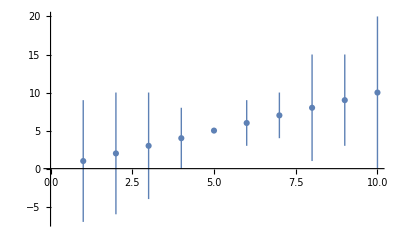

```mathematica
ListPlot[
Table[Around[i, RandomInteger[{0, 10}]], {i, 1, 10}],
Joined->False]
```

```mathematica
FinancialData["NASDAQ:AAPL", "Bid"]
```

178.86 $

```mathematica
FinancialData["NASDAQ:AAPL", "Ask"]
```

179.10 $

```mathematica
FinancialData["NASDAQ:AAPL", "Price"]
```

178.97 $

```mathematica
FinancialData["NASDAQ:AAPL", "Properties"]
```

{AdjustedClose,AdjustedHigh,AdjustedLow,AdjustedOHLC,AdjustedOHLCV,AdjustedOpen,AdjustedRange,Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EarningsYield,EBITDA,Exchange,FloatShares,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,IPODate,Last,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,Members,Name,OHLC,OHLCV,Open,PERatio,Price,PriceToBookRatio,PriceToSalesRatio,Properties,Range,Range52Week,RawClose,RawHigh,RawLow,RawOHLC,RawOHLCV,RawOpen,RawRange,RawVolume,Return,Sector,SICCode,StandardName,Symbol,Volatility20Day,Volatility250Day,Volatility50Day,Volume,Website}

```mathematica
Map[
#->FinancialData["NASDAQ:AAPL", #]&,
FinancialData["NASDAQ:AAPL", "Properties"]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

General::stop: Further output of FinancialData::dlfail will be suppressed during this calculation.

{AdjustedClose→178.97 $,AdjustedHigh→Missing[NotAvailable],AdjustedLow→178.62 $,AdjustedOHLC→$Failed,AdjustedOHLCV→$Failed,AdjustedOpen→$Failed,AdjustedRange→{178.62 $,182.14 $},Ask→$Failed,AskSize→$Failed,Average200Day→192.02 $,Average50Day→195.75 $,AverageVolume3Month→2.94181×10^7 shares,Bid→$Failed,BidSize→100 shares,BookValuePerShare→Missing[NotAvailable],Change→Missing[NotAvailable],Change200Day→Missing[NotAvailable],Change50Day→Missing[NotAvailable],ChangeHigh52Week→Missing[NotAvailable],ChangeLow52Week→Missing[NotAvailable],CIK→0000320193,Close→178.97 $,Company→Apple,CumulativeFractionalChange→Missing[NotAvailable],CumulativeReturn→-6.82071×10^-7 %,Dividend→0.77 $,DividendPerShare→2.96 $,DividendYield→1.65391 %,EarningsPerShare→11.99 $,EarningsYield→6.69945 %,EBITDA→77345000000 $,Exchange→Nasdaq,FloatShares→4601075000,FractionalChange→Missing[NotAvailable],FractionalChange200Day→-6.79554 %,FractionalChange50Day→-8.57235 %,FractionalChangeHigh52Week→-23.3435 %,FractionalChangeLow52Week→26.0352 %,High→182.14 $,High52Week→233.47 $,IPODate→Day: Fri 12 Dec 1980,Last→178.97 $,LastTradeSize→1196804 shares,LatestTrade→{Fri 24 May 2019 13:00:00GMT-7.,178.97 $},Lookup→{NASDAQ:AAPL},Low→178.62 $,Low52Week→142.00 $,MarketCap→8.234543983665466e11 $,Members→Missing[NotAvailable],Name→Apple,OHLC→{180.20 $,182.14 $,178.62 $,178.97 $},OHLCV→{180.20 $,182.14 $,178.62 $,178.97 $,23714686 shares},Open→180.20 $,PERatio→14.9266,Price→178.97 $,PriceToBookRatio→Missing[NotAvailable],PriceToSalesRatio→Missing[NotAvailable],Properties→{AdjustedClose,AdjustedHigh,AdjustedLow,AdjustedOHLC,AdjustedOHLCV,AdjustedOpen,AdjustedRange,Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EarningsYield,EBITDA,Exchange,FloatShares,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,IPODate,Last,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,Members,Name,OHLC,OHLCV,Open,PERatio,Price,PriceToBookRatio,PriceToSalesRatio,Properties,Range,Range52Week,RawClose,RawHigh,RawLow,RawOHLC,RawOHLCV,RawOpen,RawRange,RawVolume,Return,Sector,SICCode,StandardName,Symbol,Volatility20Day,Volatility250Day,Volatility50Day,Volume,Website},Range→{178.62 $,182.14 $},Range52Week→{142.00 $,233.47 $},RawClose→178.97 $,RawHigh→182.14 $,RawLow→178.62 $,RawOHLC→{180.20 $,182.14 $,178.62 $,178.97 $},RawOHLCV→{180.20 $,182.14 $,178.62 $,178.97 $,2.37147×10^7 shares},RawOpen→180.20 $,RawRange→{178.62 $,182.14 $},RawVolume→2.37147×10^7 shares,Return→-6.82071×10^-7 %,Sector→ConsumerElectronics,SICCode→3571,StandardName→NASDAQ:AAPL,Symbol→NASDAQ:AAPL,Volatility20Day→36.4365 %,Volatility250Day→30.8592 %,Volatility50Day→27.285 %,Volume→23714686 shares,Website→http://www.apple.com}

```mathematica
Column@%
```

AdjustedClose→178.97 $
AdjustedHigh→Missing[NotAvailable]
AdjustedLow→178.62 $
AdjustedOHLC→$Failed
AdjustedOHLCV→$Failed
AdjustedOpen→$Failed
AdjustedRange→{178.62 $,182.14 $}
Ask→$Failed
AskSize→$Failed
Average200Day→192.02 $
Average50Day→195.75 $
AverageVolume3Month→2.94181×10^7 shares
Bid→$Failed
BidSize→100 shares
BookValuePerShare→Missing[NotAvailable]
Change→Missing[NotAvailable]
Change200Day→Missing[NotAvailable]
Change50Day→Missing[NotAvailable]
ChangeHigh52Week→Missing[NotAvailable]
ChangeLow52Week→Missing[NotAvailable]
CIK→0000320193
Close→178.97 $
Company→Apple
CumulativeFractionalChange→Missing[NotAvailable]
CumulativeReturn→-6.82071×10^-7 %
Dividend→0.77 $
DividendPerShare→2.96 $
DividendYield→1.65391 %
EarningsPerShare→11.99 $
EarningsYield→6.69945 %
EBITDA→77345000000 $
Exchange→Nasdaq
FloatShares→4601075000
FractionalChange→Missing[NotAvailable]
FractionalChange200Day→-6.79554 %
FractionalChange50Day→-8.57235 %
FractionalChangeHigh52Week→-23.3435 %
FractionalChangeLow52Week→26.0352 %
High→182.14 $
High52Week→233.47 $
IPODate→Day: Fri 12 Dec 1980
Last→178.97 $
LastTradeSize→1196804 shares
LatestTrade→{Fri 24 May 2019 13:00:00GMT-7.,178.97 $}
Lookup→{NASDAQ:AAPL}
Low→178.62 $
Low52Week→142.00 $
MarketCap→8.234543983665466e11 $
Members→Missing[NotAvailable]
Name→Apple
OHLC→{180.20 $,182.14 $,178.62 $,178.97 $}
OHLCV→{180.20 $,182.14 $,178.62 $,178.97 $,23714686 shares}
Open→180.20 $
PERatio→14.9266
Price→178.97 $
PriceToBookRatio→Missing[NotAvailable]
PriceToSalesRatio→Missing[NotAvailable]
Properties→{AdjustedClose,AdjustedHigh,AdjustedLow,AdjustedOHLC,AdjustedOHLCV,AdjustedOpen,AdjustedRange,Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EarningsYield,EBITDA,Exchange,FloatShares,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,IPODate,Last,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,Members,Name,OHLC,OHLCV,Open,PERatio,Price,PriceToBookRatio,PriceToSalesRatio,Properties,Range,Range52Week,RawClose,RawHigh,RawLow,RawOHLC,RawOHLCV,RawOpen,RawRange,RawVolume,Return,Sector,SICCode,StandardName,Symbol,Volatility20Day,Volatility250Day,Volatility50Day,Volume,Website}
Range→{178.62 $,182.14 $}
Range52Week→{142.00 $,233.47 $}
RawClose→178.97 $
RawHigh→182.14 $
RawLow→178.62 $
RawOHLC→{180.20 $,182.14 $,178.62 $,178.97 $}
RawOHLCV→{180.20 $,182.14 $,178.62 $,178.97 $,2.37147×10^7 shares}
RawOpen→180.20 $
RawRange→{178.62 $,182.14 $}
RawVolume→2.37147×10^7 shares
Return→-6.82071×10^-7 %
Sector→ConsumerElectronics
SICCode→3571
StandardName→NASDAQ:AAPL
Symbol→NASDAQ:AAPL
Volatility20Day→36.4365 %
Volatility250Day→30.8592 %
Volatility50Day→27.285 %
Volume→23714686 shares
Website→http://www.apple.com

```mathematica
Plot3D[
√(x^2-y^2), {x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[
√(x^2-y^2), {x,y}∈Disk[{0,0}, 3]]
```

-Graphics3D-

```mathematica
Plot3D[
√(x^2+y^2), {x,y}∈Disk[{0,0}, 3]]
```

-Graphics3D-

```mathematica
Plot3D[
Exp[Sin[x y]], {x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[
Exp[Sin[x y]], {x,y}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
Plot3D[
Exp[Sin[x y]], {x,y}∈Disk[{0,0},4]]
```

-Graphics3D-

```mathematica
FunctionCompile[#^2&]
```

FunctionCompile::fun: Argument #1^2& is expected to be a Function.

FunctionCompile[#1^2&]

```mathematica
FunctionCompile[Function[{x,y}, x^y]]
```

LibraryFunction::load: The library /usr/local/Wolfram/Mathematica/12.0/SystemFiles/Components/LLVMLink/LLVMResources/Linux-x86-64/lib/libLLVM.so cannot be loaded.

Throw::nocatch: Uncaught Throw[{Could not load library LLVM,libtinfo.so.5: cannot open shared object file: No such file or directory}] returned to top level.

Hold[Throw[{Could not load library LLVM,libtinfo.so.5: cannot open shared object file: No such file or directory}]]

```mathematica
FunctionCompile[Function[{x,y}, x^y]]
```

Compile::err: TypeError. Function Power: multiple satisfiable instances of the type {v9229, v9230}→v9227 found in the list of alternatives {∀(v4234, v4235) : (Predicate[v4234 ∈ MemberQ[AbstractType[FloatingPoint]]], Predicate[v4235 ∈ MemberQ[AbstractType[Real]]])⇒{v4234, v4235}→v4234, ∀(v4241, v4242) : (Predicate[v4241 ∈ MemberQ[AbstractType[Real]]], Predicate[v4242 ∈ MemberQ[AbstractType[FloatingPoint]]])⇒{v4241, v4242}→v4242, ∀(v4248, v4249) : (Predicate[v4248 ∈ MemberQ[AbstractType[Integral]]], Predicate[v4249 ∈ MemberQ[AbstractType[Integral]]])⇒{v4248, v4249}→TypeJoin[v4248, v4249], ∀(v4256, v4257) : (Predicate[v4256 ∈ MemberQ[AbstractType[FloatingPoint]]], Predicate[v4257 ∈ MemberQ[AbstractType[FloatingPoint]]])⇒{v4256, v4257}→TypeJoin[v4256, v4257], ∀(v7233, v7234, v7235) : (Predicate[v7233 ∈ MemberQ[AbstractType[Number]]])⇒{v7233, PackedArray[v7234, v7235]}→PackedArray[TypeJoin[v7233, v7234], v7235], ∀(v7243, v7244, v7245) : (Predicate[v7245 ∈ MemberQ[AbstractType[Number]]])⇒{PackedArray[v7243, v7244], v7245}→PackedArray[TypeJoin[v7243, v7245], v7244], ∀(v7253, v7254, v7255, v7256) : ()⇒{PackedArray[v7253, v7254], PackedArray[v7255, v7256]}→PackedArray[TypeJoin[v7253, v7255], TypeEvaluate[Max, {v7254,v7256}]]}

Failure[…]

```mathematica
cf=FunctionCompile[Function[Typed[arg,"MachineInteger"],arg+1]]
```

CompiledCodeFunction[…]

```mathematica
Out[38][9]
```

10

```mathematica
Information[Out[38]]
```

Compiled Code Function

```mathematica
eqn1=2 x+3 y==5
eqn2=x-y==5
```

2 x+3 y==5

x-y==5

```mathematica
MultiplySides[eqn2,2]//Expand
```

2 x-2 y==10

```mathematica
SubtractSides[eqn1,%]
```

5 y==-5

```mathematica
DivideSides[%,5]
```

y==-1

```mathematica
MultiplySides[%,-3]
```

-3 y==3

```mathematica
a==1/(a+1)
```

a==1/(1+a)

```mathematica
MultiplySides[a==1/(1+a),b]
```

Piecewise[{{a b==b/(1+a), b≠0}, {a==1/(1+a), True}}]

```mathematica
PiecewiseExpand[Piecewise[{{a b==b/(1+a),b≠0}},a==1/(1+a)]]
```

(a-1/(1+a)==0&&b==0)||(b≠0&&a b-b/(1+a)==0)

```mathematica
D[Piecewise[{{a b==b/(1+a),b≠0}},a==1/(1+a)], a]
```

1+1/(1+a)^2==0||(0&&b+b/(1+a)^2==0)

```mathematica
FullSimplify[Piecewise[{{a b==b/(1+a),b≠0}},a==1/(1+a)]]
```

a==1/(1+a)

```mathematica
PiecewiseExpand[Piecewise[{{a b==b/(1+a),b≠0}},a==1/(1+a)]]
```

(a-1/(1+a)==0&&b==0)||(b≠0&&a b-b/(1+a)==0)

```mathematica
a==1/(1+a)
```

a==1/(1+a)

```mathematica
ApplySides[Exp,a==b]
```

ⅇ^a==ⅇ^b

```mathematica
ApplySides[Log,a==b==c]
```

Log[a]==Log[b]==Log[c]

```mathematica
ApplySides[Sin,ConditionalExpression[x==a/b,b≠0]]
```

ConditionalExpression[Sin[x]==Sin[a/b],b≠0]

```mathematica
ApplySides[f, Piecewise[{{x>-b/a, a>0}, {-b/a>x, a<0}, {a x>-b, True}}]]
```

Piecewise[{{f[x]>f[-b/a], a>0}, {f[-b/a]>f[x], a<0}, {f[a x]>f[-b], True}}]

```mathematica
ApplySides[f, Piecewise[{{x>-b/a, a>0}, {-b/a>x, a<0}, {a x>-b, True}}]]
```

Piecewise[{{f[x]>f[-b/a], a>0}, {f[-b/a]>f[x], a<0}, {f[a x]>f[-b], True}}]

```mathematica
Column[axioms=AxiomaticTheory[{"BooleanAxioms",<|"And"->and,"Or"->or,"Not"->not|>}]]
```

∀_{a,b}and[a,b]==and[b,a]
∀_{a,b}or[a,b]==or[b,a]
∀_{a,b}and[a,or[b,not[b]]]==a
∀_{a,b}or[a,and[b,not[b]]]==a
∀_{a,b,c}and[a,or[b,c]]==or[and[a,b],and[a,c]]
∀_{a,b,c}or[a,and[b,c]]==and[or[a,b],or[a,c]]

```mathematica
proof=FindEquationalProof[ForAll[{a,b},or[not[or[not[a],b]],not[or[not[a],not[b]]]]==a],axioms]
```

ProofObject[…]

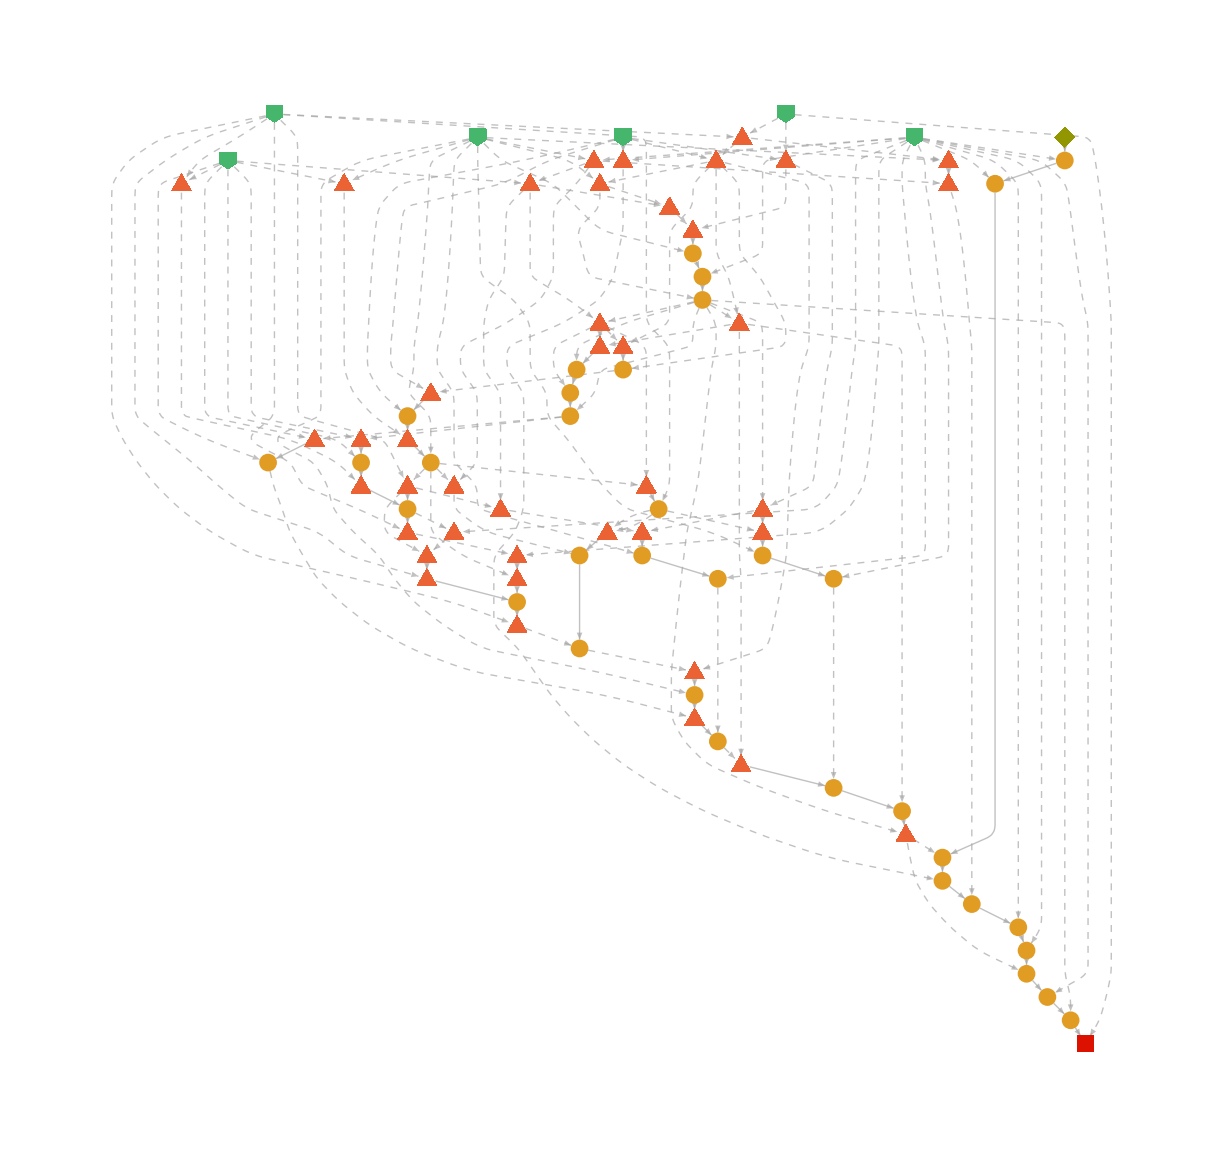

```mathematica
proof["ProofGraph"]
```

```mathematica
proof["ProofDataset"]
```

Dataset[<>]

```mathematica
presburgerArithmetic={ForAll[x,plus[x,0]==x],ForAll[x,plus[x,neg[x]]==0],ForAll[{x,y,z},plus[plus[x,y],z]==plus[x,plus[y,z]]]};
```

```mathematica
proof=FindEquationalProof[ForAll[x,neg[neg[x]]==x],presburgerArithmetic]
```

ProofObject[…]

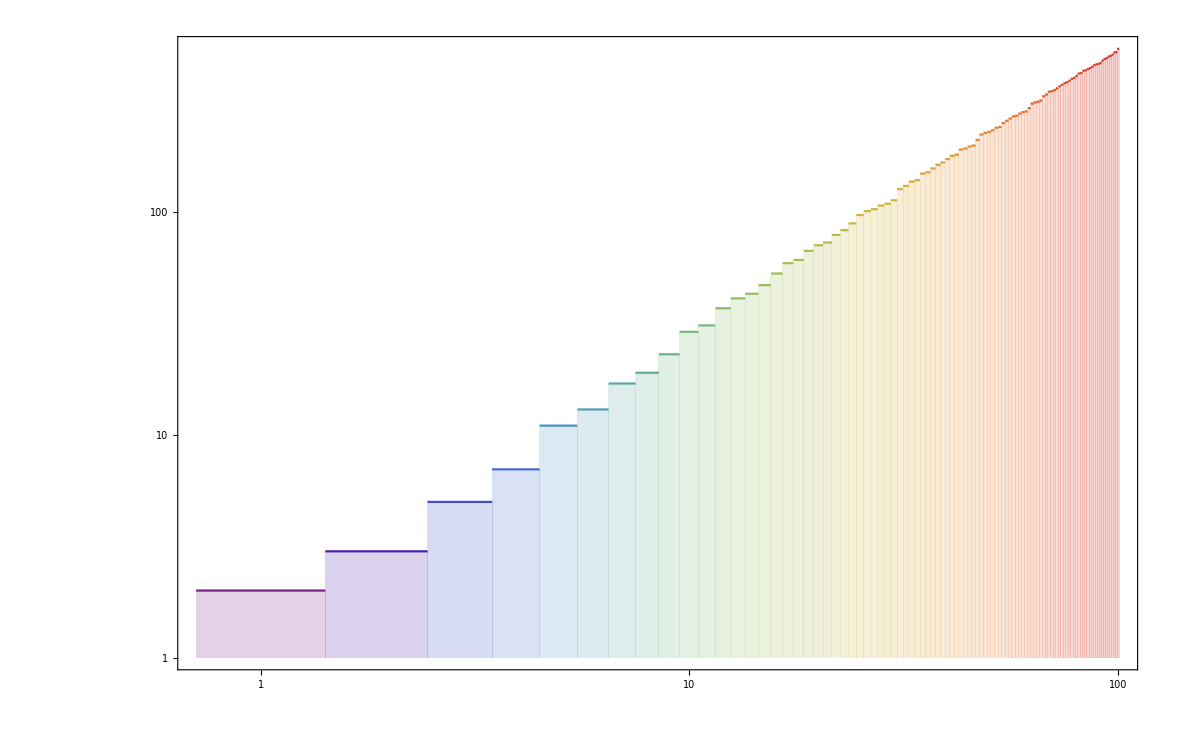

```mathematica
DiscretePlot[Prime[x],{x,1,100},ScalingFunctions->{"Log","Log"},Sequence[ExtentSize->Full,ColorFunction->"Rainbow",Frame->True]]
```

```mathematica
DiscretePlot3D[GCD[x,y],{x,25},{y,25},ScalingFunctions->"Log",Sequence[ExtentSize->Full,PlotTheme->"Scientific",ImageSize->250,ColorFunction->"Rainbow"]]
```

-Graphics3D-

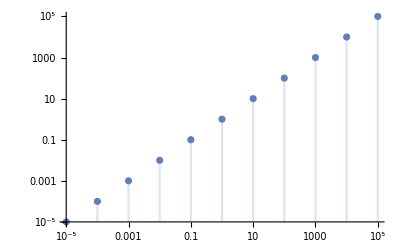

```mathematica
DiscretePlot[x,{x,10^Range[-5,5]},ScalingFunctions->{"Log","Log"}]
```

```mathematica
ListPointPlot3D[EntityValue[EntityClass["Star",{EntityProperty["Star","DistanceFromEarth"]->TakeSmallest[25]}],{"Mass","Radius","DistanceFromEarth"},"EntityAssociation"],TargetUnits->{"Kilograms","Kilometers","LightYears"},ScalingFunctions->{"Log","Log",None},Sequence[PlotTheme->"Scientific",ImageSize->400,AxesLabel->Automatic,BoxRatios->{1,1,1}]]
```

-Graphics3D-

```mathematica
Trace[ListPointPlot3D[EntityValue[EntityClass["Star",{EntityProperty["Star","DistanceFromEarth"]->TakeSmallest[25]}],{"Mass","Radius","DistanceFromEarth"},"EntityAssociation"],TargetUnits->{"Kilograms","Kilometers","LightYears"},ScalingFunctions->{"Log","Log",None},Sequence[PlotTheme->"Scientific",ImageSize->400,AxesLabel->Automatic,BoxRatios->{1,1,1}]]]
```

$Aborted[]

```mathematica
wd=Normal[WeatherForecastData["Temperature"]];
```

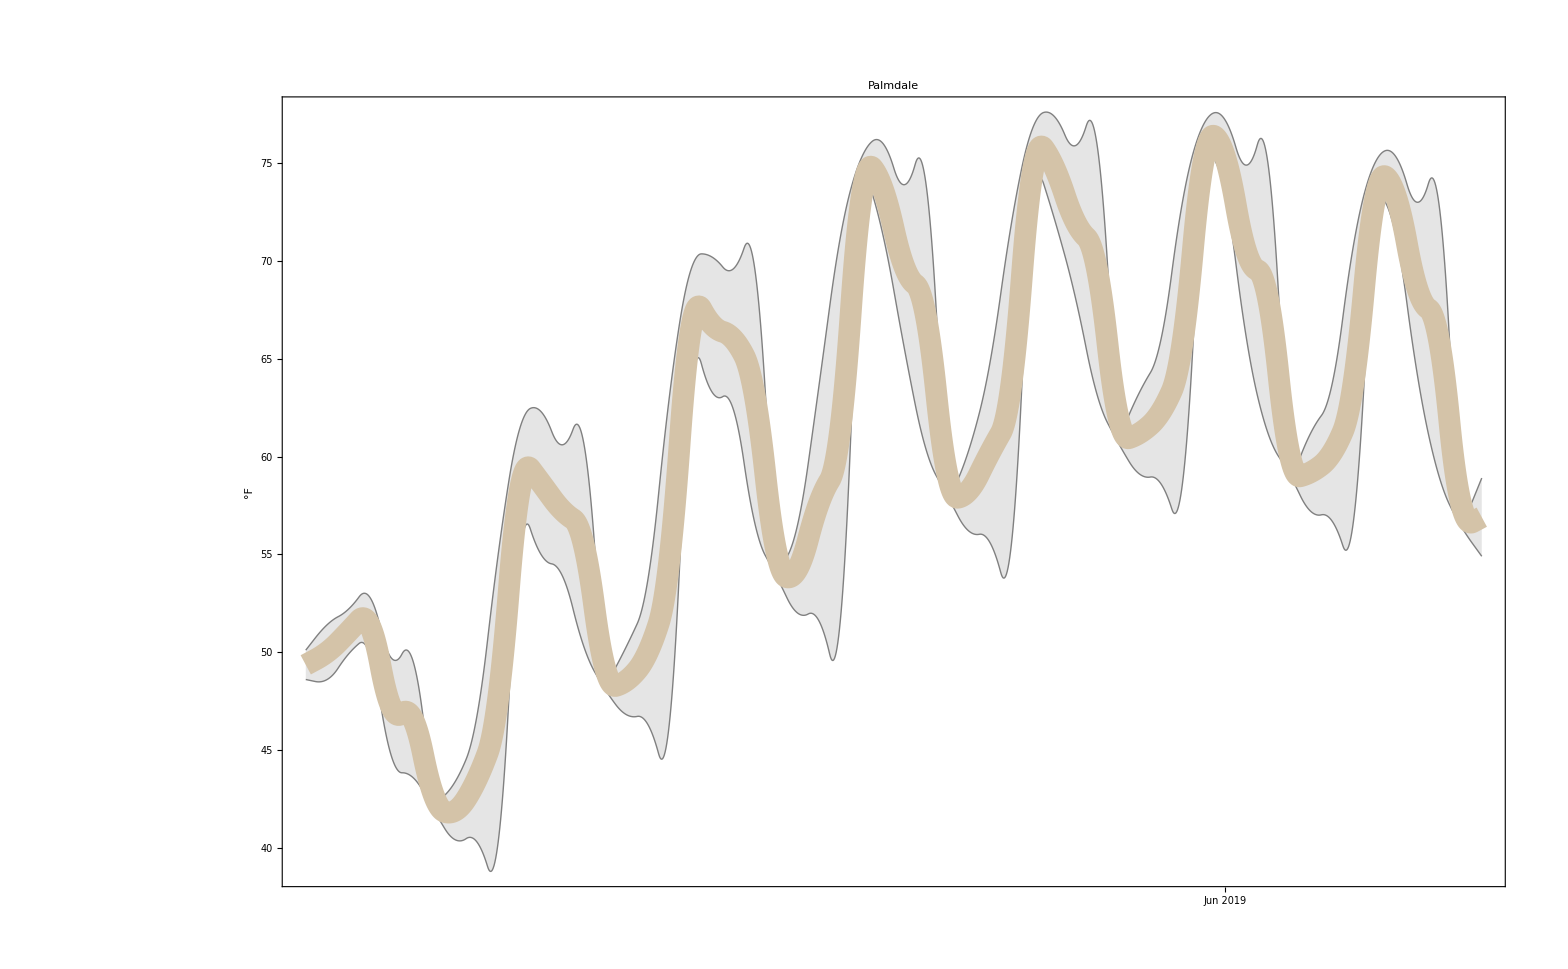

```mathematica
DateListPlot[wd,IntervalMarkers->"Bands",Sequence[AxesLabel->Automatic,ImageSize->450,PlotTheme->"Detailed",FrameLabel->Automatic,IntervalMarkersStyle->{Thin,Gray},ColorFunction->"TemperatureMap",InterpolationOrder->Automatic,PlotRange->All,PlotStyle->Thickness[0.01],PlotLabel->First[GeoNearest[Entity["City"],Here]],LabelStyle->16]]
```

```mathematica
Normal[WeatherForecastData["Temperature"]]
```

{{Sun 26 May 2019 15:00:00GMT-7.,(48.6to50.1) °F},{Sun 26 May 2019 18:00:00GMT-7.,(48.6to51.4) °F},{Sun 26 May 2019 21:00:00GMT-7.,(49.9to52.2) °F},{Mon 27 May 2019 00:00:00GMT-7.,(49.9to52.8) °F},{Mon 27 May 2019 03:00:00GMT-7.,(44.7to49.7) °F},{Mon 27 May 2019 06:00:00GMT-7.,(43.6to49.6) °F},{Mon 27 May 2019 09:00:00GMT-7.,(41.9to43.4) °F},{Mon 27 May 2019 12:00:00GMT-7.,(40.4to43.4) °F},{Mon 27 May 2019 15:00:00GMT-7.,(40.3to46.7) °F},{Mon 27 May 2019 18:00:00GMT-7.,(40.3to55.) °F},{Mon 27 May 2019 21:00:00GMT-7.,(55.to61.4) °F},{Tue 28 May 2019 00:00:00GMT-7.,(55.to62.3) °F},{Tue 28 May 2019 03:00:00GMT-7.,(53.9to60.6) °F},{Tue 28 May 2019 06:00:00GMT-7.,(50.3to60.7) °F},{Tue 28 May 2019 09:00:00GMT-7.,(48.1to50.3) °F},{Tue 28 May 2019 12:00:00GMT-7.,(46.8to50.3) °F},{Tue 28 May 2019 15:00:00GMT-7.,(46.3to53.7) °F},{Tue 28 May 2019 18:00:00GMT-7.,(46.3to63.) °F},{Tue 28 May 2019 21:00:00GMT-7.,(63.3to69.5) °F},{Wed 29 May 2019 00:00:00GMT-7.,(63.3to70.2) °F},{Wed 29 May 2019 03:00:00GMT-7.,(62.4to69.6) °F},{Wed 29 May 2019 06:00:00GMT-7.,(56.6to69.6) °F},{Wed 29 May 2019 09:00:00GMT-7.,(53.9to56.5) °F},{Wed 29 May 2019 12:00:00GMT-7.,(52.to56.5) °F},{Wed 29 May 2019 15:00:00GMT-7.,(51.6to63.6) °F},{Wed 29 May 2019 18:00:00GMT-7.,(51.6to71.2) °F},{Wed 29 May 2019 21:00:00GMT-7.,(71.3to75.3) °F},{Thu 30 May 2019 00:00:00GMT-7.,(71.3to76.) °F},{Thu 30 May 2019 03:00:00GMT-7.,(65.5to73.9) °F},{Thu 30 May 2019 06:00:00GMT-7.,(60.4to74.) °F},{Thu 30 May 2019 09:00:00GMT-7.,(58.to60.3) °F},{Thu 30 May 2019 12:00:00GMT-7.,(56.2to60.3) °F},{Thu 30 May 2019 15:00:00GMT-7.,(55.6to64.8) °F},{Thu 30 May 2019 18:00:00GMT-7.,(55.5to71.9) °F},{Thu 30 May 2019 21:00:00GMT-7.,(72.3to76.8) °F},{Fri 31 May 2019 00:00:00GMT-7.,(72.2to77.4) °F},{Fri 31 May 2019 03:00:00GMT-7.,(68.1to75.9) °F},{Fri 31 May 2019 06:00:00GMT-7.,(63.2to76.) °F},{Fri 31 May 2019 09:00:00GMT-7.,(60.7to63.4) °F},{Fri 31 May 2019 12:00:00GMT-7.,(59.1to63.3) °F},{Fri 31 May 2019 15:00:00GMT-7.,(58.6to66.) °F},{Fri 31 May 2019 18:00:00GMT-7.,(58.6to73.) °F},{Fri 31 May 2019 21:00:00GMT-7.,(73.3to77.) °F},{Sat 1 Jun 2019 00:00:00GMT-7.,(73.4to77.2) °F},{Sat 1 Jun 2019 03:00:00GMT-7.,(66.to74.9) °F},{Sat 1 Jun 2019 06:00:00GMT-7.,(61.2to75.) °F},{Sat 1 Jun 2019 09:00:00GMT-7.,(59.1to61.3) °F},{Sat 1 Jun 2019 12:00:00GMT-7.,(57.2to61.2) °F},{Sat 1 Jun 2019 15:00:00GMT-7.,(56.7to63.7) °F},{Sat 1 Jun 2019 18:00:00GMT-7.,(56.7to70.8) °F},{Sat 1 Jun 2019 21:00:00GMT-7.,(71.2to75.) °F},{Sun 2 Jun 2019 00:00:00GMT-7.,(71.2to75.3) °F},{Sun 2 Jun 2019 03:00:00GMT-7.,(64.1to73.) °F},{Sun 2 Jun 2019 06:00:00GMT-7.,(59.to72.9) °F},{Sun 2 Jun 2019 09:00:00GMT-7.,(56.5to59.) °F},{Sun 2 Jun 2019 12:00:00GMT-7.,(54.9to58.9) °F}}

```mathematica
f[z_]:=Gamma[z-I]^2/Gamma[z+I]^2
```

```mathematica
textureSphere=Texture[Rasterize[ComplexPlot[f[Cot[Im[w]] Exp[I Re[w]]],{w,-π,π+π/2 I},Sequence[ColorFunction->"CyclicLogAbsArg",Frame->False,PlotRangePadding->0,BoundaryStyle->None]],ImageResolution->400]];
```

```mathematica
sphere=SphericalPlot3D[Cos[ϕ],{ϕ,0,π/2},{θ,-π,π},TextureCoordinateFunction->({#5,#4}&),PlotStyle->Directive[textureSphere],Sequence[Mesh->{{0.5}},MeshFunctions->{#3&},MeshStyle->Directive[Thick,Black],PlotPoints->40,Lighting->"Neutral",ViewPoint->{-2,-2,1.5},BoundaryStyle->None]]
```

-Graphics3D-

```mathematica
Subscript[ℛ,1]=Octahedron[];
Subscript[ℛ,2]=Polyhedron[{{0.,2^Rational[-1,2],0.},{2^Rational[-1,2],0.,0.},{0.,-2^Rational[-1,2],0.},{-2^Rational[-1,2],0.,0.},{0.,0.,2^Rational[-1,2]},{0.,0.,-2^Rational[-1,2]}},{{5,2,1},{5,3,2},{5,4,3},{4,5,1},{2,6,1},{2,3,6},{4,6,3},{1,6,4}}];
```

```mathematica
RegionEqual[Subscript[ℛ,1],Subscript[ℛ,2]]
```

True

```mathematica
Graphics3D[{Opacity[.5],Red,Subscript[ℛ,1],Blue,Subscript[ℛ,2]}]
```

-Graphics3D-

```mathematica
Entity["Financial","NYSE:WMT"][EntityProperty["Financial","Last"]]
```

{Fri 24 May 2019 13:00:00GMT-7.,102.67 $}

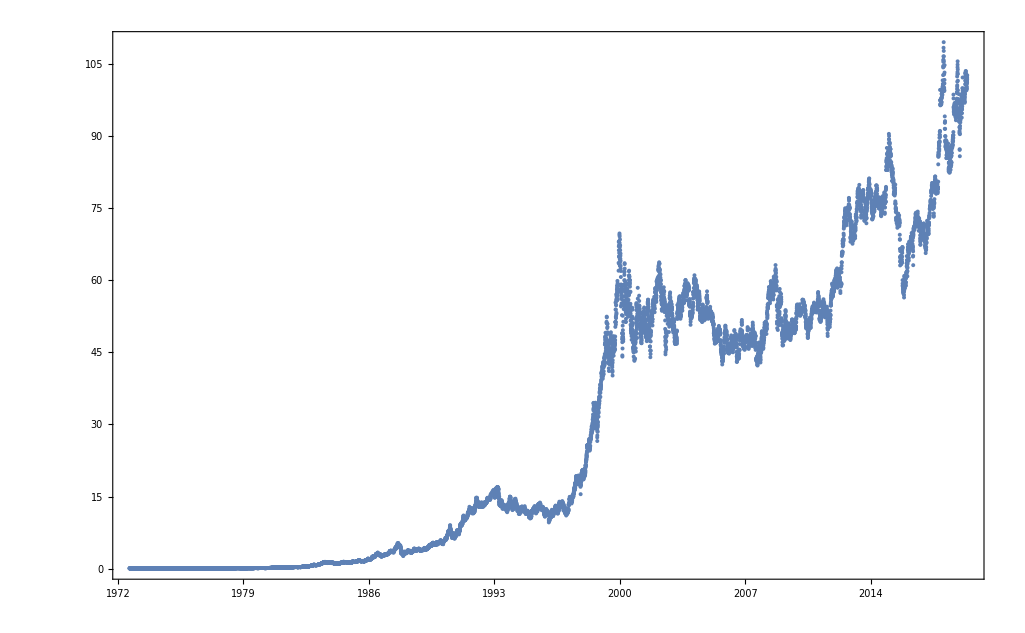

```mathematica
DateListPlot[
FinancialData[
Entity["Financial","NYSE:WMT"], "Price", All],
Joined->False]
```

```mathematica
FinancialData["NASDAQ:GOOG", "Price", All]["Properties"]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed[Properties]

```mathematica
googl=FinancialData["NASDAQ:GOOG", "Price", All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
walmart=FinancialData[
Entity["Financial","NYSE:WMT"], "Price", All]
```

TimeSeries[…]

```mathematica
walmart["DatePath"]
```

{{Fri 25 Aug 1972 00:00:00GMT-7.,0.07 $},{Mon 28 Aug 1972 00:00:00GMT-7.,0.07 $},{Tue 29 Aug 1972 00:00:00GMT-7.,0.07 $},{Wed 30 Aug 1972 00:00:00GMT-7.,0.07 $},11797,{Tue 21 May 2019 00:00:00GMT-7.,101.12 $},{Wed 22 May 2019 00:00:00GMT-7.,102.23 $},{Thu 23 May 2019 00:00:00GMT-7.,101.86 $},{Fri 24 May 2019 00:00:00GMT-7.,102.67 $}}
 |  |  |  |

```mathematica
MinimumTimeIncrement[walmart]
```

{1,Day}

```mathematica
TimeSeriesResample[walmart]
```

TimeSeries[…]

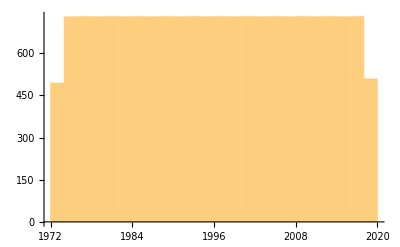

```mathematica
DateHistogram[%86]
```

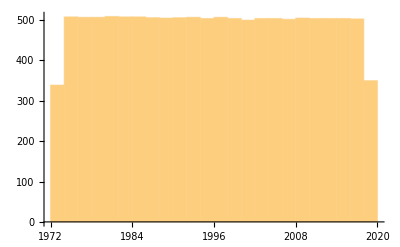

```mathematica
DateHistogram[walmart]
```

```mathematica
walmart["Properties"]
```

{DatePath,Dates,FinancialProperty,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

```mathematica
Transpose[{
walmart["Times"][[;;-2]],
Differences@
walmart["Values"]
}]
```

{{2292537600,0.00 $},{2292796800,0.00 $},{2292883200,0.00 $},{2292969600,-0.01 $},{2293056000,0.00 $},{2293142400,0.00 $},{2293488000,0.00 $},{2293574400,0.00 $},{2293660800,0.00 $},{2293747200,0.00 $},{2294006400,0.00 $},11782,{3766348800,2.37 $},{3766435200,-2.02 $},{3766694400,0.40 $},{3766780800,-0.41 $},{3766867200,1.43 $},{3766953600,-0.45 $},{3767040000,0.66 $},{3767299200,-0.40 $},{3767385600,1.11 $},{3767472000,-0.37 $},{3767558400,0.81 $}}
 |  |  |  |

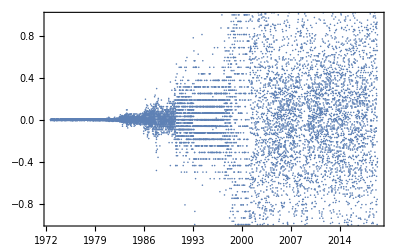

```mathematica
DateListPlot[
Out[91],
Joined->False]
```

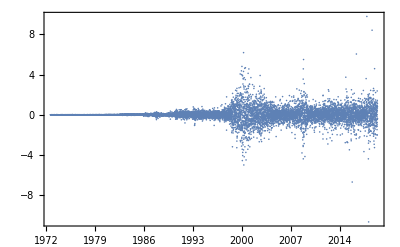

```mathematica
DateListPlot[
Out[91],
Joined->False, PlotRange->Full]
```

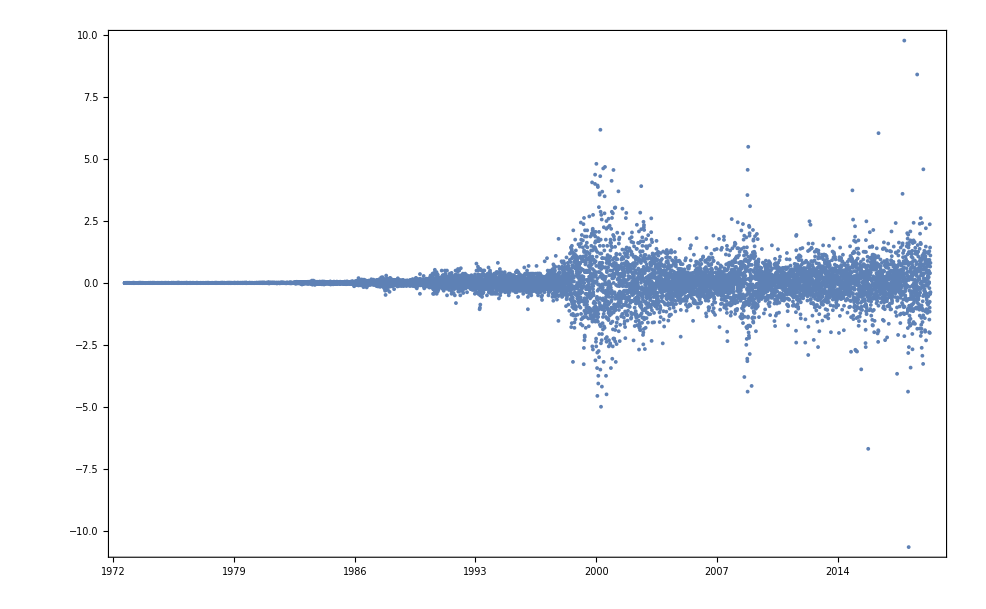

```mathematica
DateListPlot[
Out[91],
Joined->False, PlotRange->Full, Axes->True]
```

```mathematica
Take[
ReverseSortBy[
Out[91],
Last],10]
```

{{3719692800,9.79 $},{3743280000,8.42 $},{3163449600,6.19 $},{3672518400,6.05 $},{3434054400,5.50 $},{3156105600,4.81 $},{3171830400,4.69 $},{3168633600,4.63 $},{3754598400,4.59 $},{3433017600,4.57 $}}

```mathematica
Column@
Take[
ReverseSortBy[
Out[91],
Last],10]
```

{3719692800,9.79 $}
{3743280000,8.42 $}
{3163449600,6.19 $}
{3672518400,6.05 $}
{3434054400,5.50 $}
{3156105600,4.81 $}
{3171830400,4.69 $}
{3168633600,4.63 $}
{3754598400,4.59 $}
{3433017600,4.57 $}

```mathematica
Transpose[{
walmart["Dates"][[;;-2]],
Differences@
walmart["Values"]
}]
```

{{Fri 25 Aug 1972 00:00:00GMT-7.,0.00 $},{Mon 28 Aug 1972 00:00:00GMT-7.,0.00 $},{Tue 29 Aug 1972 00:00:00GMT-7.,0.00 $},{Wed 30 Aug 1972 00:00:00GMT-7.,-0.01 $},11796,{Mon 20 May 2019 00:00:00GMT-7.,-0.40 $},{Tue 21 May 2019 00:00:00GMT-7.,1.11 $},{Wed 22 May 2019 00:00:00GMT-7.,-0.37 $},{Thu 23 May 2019 00:00:00GMT-7.,0.81 $}}
 |  |  |  |

```mathematica
Column@
Take[
ReverseSortBy[
Out[97],
Last],10]
```

{Wed 15 Nov 2017 00:00:00GMT-7.,9.79 $}
{Wed 15 Aug 2018 00:00:00GMT-7.,8.42 $}
{Fri 31 Mar 2000 00:00:00GMT-7.,6.19 $}
{Wed 18 May 2016 00:00:00GMT-7.,6.05 $}
{Mon 27 Oct 2008 00:00:00GMT-7.,5.50 $}
{Thu 6 Jan 2000 00:00:00GMT-7.,4.81 $}
{Thu 6 Jul 2000 00:00:00GMT-7.,4.69 $}
{Tue 30 May 2000 00:00:00GMT-7.,4.63 $}
{Mon 24 Dec 2018 00:00:00GMT-7.,4.59 $}
{Wed 15 Oct 2008 00:00:00GMT-7.,4.57 $}

```mathematica
Column@
Take[
ReverseSortBy[
Out[97],
Last],50]
```

{Wed 15 Nov 2017 00:00:00GMT-7.,9.79 $}
{Wed 15 Aug 2018 00:00:00GMT-7.,8.42 $}
{Fri 31 Mar 2000 00:00:00GMT-7.,6.19 $}
{Wed 18 May 2016 00:00:00GMT-7.,6.05 $}
{Mon 27 Oct 2008 00:00:00GMT-7.,5.50 $}
{Thu 6 Jan 2000 00:00:00GMT-7.,4.81 $}
{Thu 6 Jul 2000 00:00:00GMT-7.,4.69 $}
{Tue 30 May 2000 00:00:00GMT-7.,4.63 $}
{Mon 24 Dec 2018 00:00:00GMT-7.,4.59 $}
{Wed 15 Oct 2008 00:00:00GMT-7.,4.57 $}
{Tue 2 Jan 2001 00:00:00GMT-7.,4.56 $}
{Fri 10 Dec 1999 00:00:00GMT-7.,4.38 $}
{Tue 28 Mar 2000 00:00:00GMT-7.,4.31 $}
{Fri 24 Nov 2000 00:00:00GMT-7.,4.13 $}
{Thu 7 Oct 1999 00:00:00GMT-7.,4.06 $}
{Wed 8 Dec 1999 00:00:00GMT-7.,4.00 $}
{Mon 31 Jan 2000 00:00:00GMT-7.,3.94 $}
{Tue 13 Aug 2002 00:00:00GMT-7.,3.91 $}
{Mon 7 Feb 2000 00:00:00GMT-7.,3.87 $}
{Wed 12 Nov 2014 00:00:00GMT-7.,3.74 $}
{Tue 17 Apr 2001 00:00:00GMT-7.,3.70 $}
{Tue 9 May 2000 00:00:00GMT-7.,3.69 $}
{Tue 14 Mar 2000 00:00:00GMT-7.,3.63 $}
{Mon 9 Oct 2017 00:00:00GMT-7.,3.60 $}
{Wed 15 Mar 2000 00:00:00GMT-7.,3.56 $}
{Fri 10 Oct 2008 00:00:00GMT-7.,3.55 $}
{Thu 29 Jun 2000 00:00:00GMT-7.,3.50 $}
{Thu 4 Dec 2008 00:00:00GMT-7.,3.10 $}
{Mon 28 Feb 2000 00:00:00GMT-7.,3.06 $}
{Fri 9 Feb 2001 00:00:00GMT-7.,3.05 $}
{Tue 30 Jan 2001 00:00:00GMT-7.,3.03 $}
{Wed 11 Jul 2001 00:00:00GMT-7.,3.00 $}
{Tue 28 Nov 2000 00:00:00GMT-7.,2.88 $}
{Wed 5 Apr 2000 00:00:00GMT-7.,2.88 $}
{Tue 23 Jul 2002 00:00:00GMT-7.,2.84 $}
{Mon 1 Oct 2001 00:00:00GMT-7.,2.83 $}
{Mon 26 Jun 2000 00:00:00GMT-7.,2.81 $}
{Wed 20 Dec 2000 00:00:00GMT-7.,2.81 $}
{Wed 19 Apr 2000 00:00:00GMT-7.,2.75 $}
{Wed 27 Oct 1999 00:00:00GMT-7.,2.75 $}
{Mon 9 Aug 1999 00:00:00GMT-7.,2.69 $}
{Fri 1 Dec 2000 00:00:00GMT-7.,2.63 $}
{Mon 19 Apr 1999 00:00:00GMT-7.,2.63 $}
{Fri 21 Sep 2001 00:00:00GMT-7.,2.62 $}
{Mon 29 Oct 2018 00:00:00GMT-7.,2.62 $}
{Fri 14 Mar 2003 00:00:00GMT-7.,2.61 $}
{Wed 20 Sep 2000 00:00:00GMT-7.,2.59 $}
{Mon 12 Nov 2007 00:00:00GMT-7.,2.58 $}
{Fri 28 Apr 2000 00:00:00GMT-7.,2.56 $}
{Wed 26 Nov 2014 00:00:00GMT-7.,2.56 $}

```mathematica
Column@
Take[
SortBy[
Out[97],
Last],10]
```

{Fri 16 Feb 2018 00:00:00GMT-7.,-10.67 $}
{Tue 13 Oct 2015 00:00:00GMT-7.,-6.70 $}
{Thu 13 Apr 2000 00:00:00GMT-7.,-5.00 $}
{Thu 27 Jan 2000 00:00:00GMT-7.,-4.56 $}
{Tue 8 Aug 2000 00:00:00GMT-7.,-4.50 $}
{Fri 2 Feb 2018 00:00:00GMT-7.,-4.39 $}
{Tue 14 Oct 2008 00:00:00GMT-7.,-4.39 $}
{Tue 2 May 2000 00:00:00GMT-7.,-4.19 $}
{Wed 7 Jan 2009 00:00:00GMT-7.,-4.16 $}
{Tue 15 Feb 2000 00:00:00GMT-7.,-4.06 $}

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock, "Price",All]},
Column@
Take[
SortBy[
ts,
Last],10]]]
```

Last::normal: Nonatomic expression expected at position 1 in Last[TimeSeries].

Last::normal: Nonatomic expression expected at position 1 in Last[True].

Last::normal: Nonatomic expression expected at position 1 in Last[12.].

General::stop: Further output of Last::normal will be suppressed during this calculation.

TemporalData::nonopt: Options expected (instead of {«1»}) beyond position 2 in «1». An option must be a rule or a list of rules.

Take::take: Cannot take positions 1 through 10 in «1».

Column[Take[TemporalData[12.,TimeSeries,True,{{QuantityArray[…]},{{{3072643200,3072729600,3072988800,3073075200,3073161600,3073248000,3073334400,3073680000,3073766400,3073852800,3073939200,3074198400,3074284800,3074371200,3074457600,3074544000,3074803200,3074889600,3074976000,3075062400,3075148800,3075408000,3075494400,3075580800,3075667200,3075753600,3076012800,3076099200,3076185600,3076272000,3076358400,3076617600,3076704000,3076790400,3076876800,3077222400,3077308800,3077395200,3077481600,3077568000,3077827200,3077913600,3078000000,3078086400,3078172800,3078432000,3078518400,3078604800,3078691200,3078777600,3079036800,3079123200,3079209600,3079296000,3079382400,3079641600,3079728000,3079814400,3079900800,3079987200,3080246400,3080332800,3080419200,3080505600,3080592000,3080851200,3080937600,3081024000,3081110400,3081196800,3081456000,3081542400,3081628800,3081715200,3081801600,3082147200,3082233600,3082320000,3082406400,3082665600,3082752000,3082838400,3082924800,3083011200,3083270400,3083356800,3083443200,3083529600,3083616000,3083875200,3083961600,3084048000,3084134400,3084220800,3084480000,3084566400,3084652800,3084739200,3084825600,3085084800,3085171200,3085257600,3085344000,3085430400,3085689600,3085776000,3085862400,3085948800,3086035200,3086294400,3086380800,3086467200,3086553600,3086640000,3086899200,3086985600,3087072000,3087158400,3087244800,3087504000,3087590400,3087676800,3087763200,3087849600,3088108800,3088195200,3088281600,3088368000,3088454400,3088713600,3088800000,3088886400,3088972800,3089059200,3089318400,3089404800,3089491200,3089664000,3089923200,3090009600,3090096000,3090182400,3090268800,3090528000,3090614400,3090700800,3090787200,3090873600,3091132800,3091219200,3091305600,3091392000,3091478400,3091737600,3091824000,3091910400,3092083200,3092342400,3092428800,3092515200,3092688000,3092947200,3093033600,3093120000,3093206400,3093292800,3093552000,3093638400,3093724800,3093811200,3093897600,3094243200,3094329600,3094416000,3094502400,3094761600,3094848000,3094934400,3095020800,3095107200,3095366400,3095452800,3095539200,3095625600,3095712000,3095971200,3096057600,3096144000,3096230400,3096316800,3096662400,3096748800,3096835200,3096921600,3097180800,3097267200,3097353600,3097440000,3097526400,3097785600,3097872000,3097958400,3098044800,3098131200,3098390400,3098476800,3098563200,3098649600,3098736000,3098995200,3099081600,3099168000,3099254400,3099340800,3099600000,3099686400,3099772800,3099859200,3099945600,3100204800,3100291200,3100377600,3100464000,3100550400,3100809600,3100896000,3100982400,3101068800,3101414400,3101500800,3101587200,3101673600,3101760000,3102019200,3102105600,3102192000,3102278400,3102364800,3102624000,3102710400,3102796800,3102883200,3102969600,3103228800,3103315200,3103401600,3103488000,3103574400,3103833600,3103920000,3104006400,3104092800,3104179200,3104438400,3104524800,3104611200,3104697600,3104784000,3105129600,3105216000,3105302400,3105388800,3105648000,3105734400,3105820800,3105907200,3105993600,3106252800,3106339200,3106425600,3106512000,3106598400,3106857600,3106944000,3107030400,3107116800,3107203200,3107462400,3107548800,3107635200,3107721600,3107808000,3108067200,3108153600,3108240000,3108326400,3108672000,3108758400,3108844800,3108931200,3109017600,3109276800,3109363200,3109449600,3109536000,3109622400,3109881600,3109968000,3110054400,3110140800,3110227200,3110486400,3110572800,3110659200,3110745600,3110832000,3111091200,3111177600,3111264000,3111350400,3111436800,3111696000,3111782400,3111868800,3111955200,3112041600,3112300800,3112387200,3112473600,3112560000,3112646400,3112905600,3112992000,3113078400,3113164800,3113251200,3113510400,3113596800,3113683200,3113769600,3113856000,3114201600,3114288000,3114374400,3114460800,3114720000,3114806400,3114892800,3114979200,3115065600,3115324800,3115411200,3115497600,3115584000,3115670400,3115929600,3116016000,3116102400,3116188800,3116275200,3116534400,3116620800,3116707200,3116793600,3116880000,3117139200,3117225600,3117312000,3117398400,3117484800,3117744000,3117830400,3117916800,3118003200,3118089600,3118348800,3118435200,3118521600,3118608000,3118694400,3118953600,3119040000,3119126400,3119212800,3119299200,3119558400,3119644800,3119731200,3119817600,3119904000,3120163200,3120249600,3120336000,3120422400,3120508800,3120768000,3120854400,3120940800,3121113600,3121372800,3121459200,3121545600,3121632000,3121718400,3121977600,3122064000,3122150400,3122236800,3122323200,3122582400,3122668800,3122755200,3122841600,3122928000,3123187200,3123273600,3123360000,3123446400,3123792000,3123878400,3123964800,3124051200,3124396800,3124483200,3124569600,3124656000,3124742400,3125001600,3125088000,3125174400,3125260800,3125347200,3125692800,3125779200,3125865600,3125952000,3126211200,3126297600,3126384000,3126470400,3126556800,3126816000,3126902400,3126988800,3127075200,3127161600,3127420800,3127507200,3127593600,3127680000,3127766400,3128112000,3128198400,3128284800,3128371200,3128630400,3128716800,3128803200,3128889600,3128976000,3129235200,3129321600,3129408000,3129494400,3129580800,3129840000,3129926400,3130012800,3130099200,3130185600,3130444800,3130531200,3130617600,3130704000,3130790400,3131049600,3131136000,3131222400,3131308800,3131395200,3131654400,3131740800,3131827200,3131913600,3132259200,3132345600,3132432000,3132518400,3132604800,3132864000,3132950400,3133036800,3133123200,3133209600,3133468800,3133555200,3133641600,3133728000,3133814400,3134073600,3134160000,3134246400,3134332800,3134419200,3134678400,3134764800,3134851200,3134937600,3135024000,3135283200,3135369600,3135456000,3135542400,3135628800,3135888000,3135974400,3136060800,3136147200,3136233600,3136492800,3136579200,3136665600,3136752000,3136838400,3137184000,3137270400,3137356800,3137443200,3137702400,3137788800,3137875200,3137961600,3138048000,3138307200,3138393600,3138480000,3138566400,3138652800,3138912000,3138998400,3139084800,3139171200,3139257600,3139516800,3139603200,3139689600,3139776000,3139862400,3140208000,3140294400,3140380800,3140467200,3140726400,3140812800,3140899200,3140985600,3141072000,3141331200,3141417600,3141504000,3141590400,3141676800,3141936000,3142022400,3142108800,3142195200,3142281600,3142540800,3142627200,3142713600,3142800000,3142886400,3143145600,3143232000,3143318400,3143404800,3143491200,3143750400,3143836800,3143923200,3144009600,3144096000,3144355200,3144441600,3144528000,3144614400,3144700800,3144960000,3145046400,3145132800,3145219200,3145305600,3145651200,3145737600,3145824000,3145910400,3146169600,3146256000,3146342400,3146428800,3146515200,3146774400,3146860800,3146947200,3147033600,3147120000,3147379200,3147465600,3147552000,3147638400,3147724800,3147984000,3148070400,3148156800,3148243200,3148329600,3148588800,3148675200,3148761600,3148848000,3148934400,3149193600,3149280000,3149366400,3149452800,3149539200,3149798400,3149884800,3149971200,3150057600,3150144000,3150403200,3150489600,3150576000,3150662400,3150748800,3151008000,3151094400,3151180800,3151267200,3151353600,3151612800,3151699200,3151785600,3151872000,3151958400,3152217600,3152304000,3152390400,3152563200,3152822400,3152908800,3152995200,3153081600,3153168000,3153427200,3153513600,3153600000,3153686400,3153772800,3154032000,3154118400,3154204800,3154291200,3154377600,3154636800,3154723200,3154809600,3154896000,3155241600,3155328000,3155414400,3155500800,3155587200,3155846400,3155932800,3156019200,3156105600,3156192000,3156451200,3156537600,3156624000,3156710400,3156796800,3157142400,3157228800,3157315200,3157401600,3157660800,3157747200,3157833600,3157920000,3158006400,3158265600,3158352000,3158438400,3158524800,3158611200,3158870400,3158956800,3159043200,3159129600,3159216000,3159475200,3159561600,3159648000,3159734400,3159820800,3160166400,3160252800,3160339200,3160425600,3160684800,3160771200,3160857600,3160944000,3161030400,3161289600,3161376000,3161462400,3161548800,3161635200,3161894400,3161980800,3162067200,3162153600,3162240000,3162499200,3162585600,3162672000,3162758400,3162844800,3163104000,3163190400,3163276800,3163363200,3163449600,3163708800,3163795200,3163881600,3163968000,3164054400,3164313600,3164400000,3164486400,3164572800,3164659200,3164918400,3165004800,3165091200,3165177600,3165523200,3165609600,3165696000,3165782400,3165868800,3166128000,3166214400,3166300800,3166387200,3166473600,3166732800,3166819200,3166905600,3166992000,3167078400,3167337600,3167424000,3167510400,3167596800,3167683200,3167942400,3168028800,3168115200,3168201600,3168288000,3168633600,3168720000,3168806400,3168892800,3169152000,3169238400,3169324800,3169411200,3169497600,3169756800,3169843200,3169929600,3170016000,3170102400,3170361600,3170448000,3170534400,3170620800,3170707200,3170966400,3171052800,3171139200,3171225600,3171312000,3171571200,3171744000,3171830400,3171916800,3172176000,3172262400,3172348800,3172435200,3172521600,3172780800,3172867200,3172953600,3173040000,3173126400,3173385600,3173472000,3173558400,3173644800,3173731200,3173990400,3174076800,3174163200,3174249600,3174336000,3174595200,3174681600,3174768000,3174854400,3174940800,3175200000,3175286400,3175372800,3175459200,3175545600,3175804800,3175891200,3175977600,3176064000,3176150400,3176409600,3176496000,3176582400,3176668800,3176755200,3177100800,3177187200,3177273600,3177360000,3177619200,3177705600,3177792000,3177878400,3177964800,3178224000,3178310400,3178396800,3178483200,3178569600,3178828800,3178915200,3179001600,3179088000,3179174400,3179433600,3179520000,3179606400,3179692800,3179779200,3180038400,3180124800,3180211200,3180297600,3180384000,3180643200,3180729600,3180816000,3180902400,3180988800,3181248000,3181334400,3181420800,3181507200,3181593600,3181852800,3181939200,3182025600,3182112000,3182198400,3182457600,3182544000,3182630400,3182716800,3182803200,3183062400,3183148800,3183235200,3183321600,3183408000,3183667200,3183753600,3183840000,3184012800,3184272000,3184358400,3184444800,3184531200,3184617600,3184876800,3184963200,3185049600,3185136000,3185222400,3185481600,3185568000,3185654400,3185740800,3185827200,3186086400,3186172800,3186259200,3186345600,3186432000,3186777600,3186864000,3186950400,3187036800,3187382400,3187468800,3187555200,3187641600,3187900800,3187987200,3188073600,3188160000,3188246400,3188592000,3188678400,3188764800,3188851200,3189110400,3189196800,3189283200,3189369600,3189456000,3189715200,3189801600,3189888000,3189974400,3190060800,3190320000,3190406400,3190492800,3190579200,3190665600,3190924800,3191011200,3191097600,3191184000,3191270400,3191616000,3191702400,3191788800,3191875200,3192134400,3192220800,3192307200,3192393600,3192480000,3192739200,3192825600,3192912000,3192998400,3193084800,3193344000,3193430400,3193516800,3193603200,3193689600,3193948800,3194035200,3194121600,3194208000,3194294400,3194553600,3194640000,3194726400,3194812800,3194899200,3195158400,3195244800,3195331200,3195417600,3195504000,3195763200,3195849600,3195936000,3196022400,3196368000,3196454400,3196540800,3196627200,3196713600,3196972800,3197059200,3197145600,3197232000,3197318400,3197577600,3197664000,3197750400,3197836800,3197923200,3198182400,3198268800,3198355200,3198441600,3198528000,3198787200,3198873600,3198960000,3199046400,3199132800,3199392000,3199478400,3199564800,3199651200,3199737600,3200083200,3200169600,3200256000,3200342400,3200601600,3200688000,3200774400,3200860800,3200947200,3201206400,3201292800,3201379200,3201465600,3201552000,3201811200,3201897600,3201984000,3202070400,3202156800,3202416000,3202502400,3202588800,3202675200,3202761600,3203020800,3203107200,3203280000,3203366400,3203625600,3203712000,3203798400,3203884800,3203971200,3204230400,3204316800,3204403200,3204489600,3204576000,3204835200,3204921600,3205008000,3205094400,3205180800,3205440000,3205526400,3205612800,3205699200,3205785600,3206044800,3206131200,3206217600,3206304000,3206390400,3206649600,3206736000,3206822400,3206908800,3206995200,3207254400,3207340800,3207427200,3207513600,3207600000,3207859200,3207945600,3208032000,3208118400,3208204800,3208550400,3208636800,3208723200,3208809600,3209068800,3209673600,3209760000,3209846400,3209932800,3210019200,3210278400,3210364800,3210451200,3210537600,3210624000,3210883200,3210969600,3211056000,3211142400,3211228800,3211488000,3211574400,3211660800,3211747200,3211833600,3212092800,3212179200,3212265600,3212352000,3212438400,3212697600,3212784000,3212870400,3212956800,3213043200,3213302400,3213388800,3213475200,3213561600,3213648000,3213907200,3213993600,3214080000,3214166400,3214252800,3214512000,3214598400,3214684800,3214771200,3214857600,3215116800,3215203200,3215289600,3215462400,3215721600,3215808000,3215894400,3215980800,3216067200,3216326400,3216412800,3216499200,3216585600,3216672000,3216931200,3217017600,3217104000,3217190400,3217276800,3217536000,3217622400,3217708800,3217795200,3217881600,3218140800,3218313600,3218400000,3218486400,3218745600,3218918400,3219004800,3219091200,3219350400,3219436800,3219523200,3219609600,3219696000,3219955200,3220041600,3220128000,3220214400,3220300800,3220646400,3220732800,3220819200,3220905600,3221164800,3221251200,3221337600,3221424000,3221510400,3221769600,3221856000,3221942400,3222028800,3222115200,3222374400,3222460800,3222547200,3222633600,3222720000,3223065600,3223152000,3223238400,3223324800,3223584000,3223670400,3223756800,3223843200,3223929600,3224188800,3224275200,3224361600,3224448000,3224534400,3224793600,3224880000,3224966400,3225052800,3225139200,3225398400,3225484800,3225571200,3225657600,3225744000,3226003200,3226089600,3226176000,3226262400,3226608000,3226694400,3226780800,3226867200,3226953600,3227212800,3227299200,3227385600,3227472000,3227558400,3227817600,3227904000,3227990400,3228076800,3228163200,3228422400,3228508800,3228595200,3228681600,3228768000,3229027200,3229113600,3229200000,3229286400,3229372800,3229632000,3229718400,3229804800,3229891200,3229977600,3230236800,3230323200,3230409600,3230496000,3230582400,3230841600,3230928000,3231014400,3231100800,3231187200,3231532800,3231619200,3231705600,3231792000,3232051200,3232137600,3232224000,3232310400,3232396800,3232656000,3232742400,3232828800,3232915200,3233001600,3233260800,3233347200,3233433600,3233520000,3233606400,3233865600,3233952000,3234038400,3234124800,3234211200,3234470400,3234556800,3234643200,3234816000,3235075200,3235161600,3235248000,3235334400,3235420800,3235680000,3235766400,3235852800,3235939200,3236025600,3236284800,3236371200,3236457600,3236544000,3236630400,3236889600,3236976000,3237062400,3237148800,3237235200,3237494400,3237580800,3237667200,3237753600,3237840000,3238099200,3238185600,3238272000,3238358400,3238444800,3238704000,3238790400,3238876800,3238963200,3239049600,3239308800,3239395200,3239481600,3239568000,3239654400,3240000000,3240086400,3240172800,3240259200,3240518400,3240604800,3240691200,3240777600,3240864000,3241123200,3241209600,3241296000,3241382400,3241468800,3241728000,3241814400,3241900800,3241987200,3242073600,3242332800,3242419200,3242505600,3242592000,3242678400,3242937600,3243024000,3243110400,3243196800,3243283200,3243542400,3243628800,3243715200,3243801600,3243888000,3244147200,3244233600,3244320000,3244406400,3244492800,3244752000,3244838400,3244924800,3245011200,3245097600,3245356800,3245443200,3245529600,3245616000,3245702400,3245961600,3246048000,3246134400,3246220800,3246307200,3246566400,3246652800,3246739200,3246825600,3246912000,3247171200,3247257600,3247344000,3247516800,3247776000,3247862400,3247948800,3248035200,3248121600,3248380800,3248467200,3248553600,3248640000,3248726400,3248985600,3249072000,3249158400,3249244800,3249331200,3249590400,3249676800,3249849600,3249936000,3250195200,3250281600,3250454400,3250540800,3250800000,3250886400,3250972800,3251059200,3251145600,3251404800,3251491200,3251577600,3251664000,3251750400,3252096000,3252182400,3252268800,3252355200,3252614400,3252700800,3252787200,3252873600,3252960000,3253219200,3253305600,3253392000,3253478400,3253564800,3253824000,3253910400,3253996800,3254083200,3254169600,3254515200,3254601600,3254688000,3254774400,3255033600,3255120000,3255206400,3255292800,3255379200,3255638400,3255724800,3255811200,3255897600,3255984000,3256243200,3256329600,3256416000,3256502400,3256588800,3256848000,3256934400,3257020800,3257107200,3257193600,3257452800,3257539200,3257625600,3257712000,3257798400,3258057600,3258144000,3258230400,3258316800,3258403200,3258662400,3258748800,3258835200,3258921600,3259008000,3259267200,3259353600,3259440000,3259526400,3259872000,3259958400,3260044800,3260131200,3260217600,3260476800,3260563200,3260649600,3260736000,3260822400,3261081600,3261168000,3261254400,3261340800,3261427200,3261686400,3261772800,3261859200,3261945600,3262032000,3262291200,3262377600,3262464000,3262550400,3262636800,3262982400,3263068800,3263155200,3263241600,3263500800,3263587200,3263673600,3263760000,3263846400,3264105600,3264192000,3264278400,3264364800,3264451200,3264710400,3264796800,3264883200,3264969600,3265056000,3265315200,3265401600,3265488000,3265574400,3265660800,3265920000,3266006400,3266092800,3266179200,3266524800,3266611200,3266697600,3266784000,3266870400,3267129600,3267216000,3267302400,3267388800,3267475200,3267734400,3267820800,3267907200,3267993600,3268080000,3268339200,3268425600,3268512000,3268598400,3268684800,3268944000,3269030400,3269116800,3269203200,3269289600,3269548800,3269635200,3269721600,3269808000,3269894400,3270153600,3270240000,3270326400,3270412800,3270499200,3270758400,3270844800,3270931200,3271017600,3271104000,3271449600,3271536000,3271622400,3271708800,3271968000,3272054400,3272140800,3272227200,3272313600,3272572800,3272659200,3272745600,3272832000,3272918400,3273177600,3273264000,3273350400,3273436800,3273523200,3273782400,3273868800,3273955200,3274041600,3274128000,3274387200,3274473600,3274560000,3274646400,3274732800,3274992000,3275078400,3275164800,3275251200,3275337600,3275596800,3275683200,3275769600,3275856000,3275942400,3276201600,3276288000,3276374400,3276460800,3276547200,3276806400,3276892800,3276979200,3277065600,3277152000,3277411200,3277497600,3277584000,3277670400,3277756800,3278016000,3278102400,3278188800,3278275200,3278361600,3278620800,3278707200,3278793600,3278966400,3279225600,3279312000,3279398400,3279484800,3279571200,3279830400,3279916800,3280003200,3280089600,3280176000,3280435200,3280521600,3280608000,3280694400,3280780800,3281040000,3281126400,3281212800,3281385600,3281644800,3281731200,3281817600,3281990400,3282249600,3282336000,3282422400,3282508800,3282595200,3282854400,3282940800,3283027200,3283113600,3283200000,3283545600,3283632000,3283718400,3283804800,3284064000,3284150400,3284236800,3284323200,3284409600,3284668800,3284755200,3284841600,3284928000,3285014400,3285273600,3285360000,3285446400,3285532800,3285619200,3285964800,3286051200,3286137600,3286224000,3286483200,3286569600,3286656000,3286742400,3286828800,3287088000,3287174400,3287260800,3287347200,3287433600,3287692800,3287779200,3287865600,3287952000,3288038400,3288297600,3288384000,3288470400,3288556800,3288643200,3288902400,3288988800,3289075200,3289161600,3289248000,3289507200,3289593600,3289680000,3289766400,3289852800,3290112000,3290198400,3290284800,3290371200,3290716800,3290803200,3290889600,3290976000,3291062400,3291321600,3291408000,3291494400,3291580800,3291667200,3291926400,3292012800,3292099200,3292185600,3292272000,3292531200,3292617600,3292704000,3292790400,3292876800,3293136000,3293222400,3293308800,3293395200,3293481600,3293740800,3293827200,3293913600,3294000000,3294086400,3294345600,3294432000,3294518400,3294604800,3294691200,3295036800,3295123200,3295209600,3295296000,3295555200,3295641600,3295728000,3295814400,3296160000,3296246400,3296332800,3296419200,3296505600,3296764800,3296851200,3296937600,3297024000,3297110400,3297369600,3297456000,3297542400,3297628800,3297715200,3298060800,3298147200,3298233600,3298320000,3298579200,3298665600,3298752000,3298838400,3298924800,3299184000,3299270400,3299356800,3299443200,3299529600,3299788800,3299875200,3299961600,3300048000,3300134400,3300393600,3300480000,3300566400,3300652800,3300739200,3300998400,3301084800,3301171200,3301257600,3301344000,3301603200,3301689600,3301776000,3301862400,3301948800,3302208000,3302294400,3302380800,3302467200,3302553600,3302812800,3302899200,3302985600,3303072000,3303158400,3303504000,3303590400,3303676800,3303763200,3304022400,3304108800,3304195200,3304281600,3304368000,3304627200,3304713600,3304800000,3304886400,3304972800,3305232000,3305318400,3305404800,3305491200,3305577600,3305836800,3305923200,3306009600,3306096000,3306182400,3306441600,3306528000,3306614400,3306700800,3306787200,3307046400,3307132800,3307219200,3307305600,3307392000,3307651200,3307737600,3307824000,3307910400,3307996800,3308256000,3308342400,3308428800,3308515200,3308601600,3308860800,3308947200,3309033600,3309120000,3309206400,3309465600,3309552000,3309638400,3309724800,3309811200,3310070400,3310156800,3310243200,3310416000,3310675200,3310761600,3310848000,3310934400,3311020800,3311280000,3311366400,3311452800,3311539200,3311625600,3311884800,3311971200,3312057600,3312144000,3312230400,3312489600,3312576000,3312662400,3312748800,3313094400,3313180800,3313267200,3313353600,3313440000,3313699200,3313785600,3313872000,3313958400,3314044800,3314304000,3314390400,3314476800,3314563200,3314649600,3314995200,3315081600,3315168000,3315254400,3315513600,3315600000,3315686400,3315772800,3315859200,3316118400,3316204800,3316291200,3316377600,3316464000,3316723200,3316809600,3316896000,3316982400,3317068800,3317328000,3317414400,3317500800,3317587200,3317673600,3318019200,3318105600,3318192000,3318278400,3318537600,3318624000,3318710400,3318796800,3318883200,3319142400,3319228800,3319315200,3319401600,3319488000,3319747200,3319833600,3319920000,3320006400,3320092800,3320352000,3320438400,3320524800,3320611200,3320956800,3321043200,3321129600,3321216000,3321302400,3321561600,3321648000,3321734400,3321820800,3321907200,3322166400,3322252800,3322339200,3322425600,3322512000,3322771200,3322857600,3322944000,3323030400,3323116800,3323376000,3323462400,3323548800,3323635200,3323721600,3323980800,3324067200,3324153600,3324240000,3324326400,3324585600,3324672000,3324758400,3324844800,3324931200,3325190400,3325276800,3325363200,3325449600,3325536000,3325795200,3325881600,3325968000,3326054400,3326140800,3326486400,3326572800,3326659200,3326745600,3327004800,3327091200,3327177600,3327264000,3327350400,3327609600,3327696000,3327782400,3327868800,3327955200,3328214400,3328300800,3328387200,3328473600,3328560000,3328819200,3328905600,3328992000,3329078400,3329164800,3329510400,3329596800,3329683200,3329769600,3330028800,3330115200,3330201600,3330288000,3330374400,3330633600,3330720000,3330806400,3330892800,3330979200,3331238400,3331324800,3331411200,3331497600,3331584000,3331843200,3331929600,3332016000,3332102400,3332188800,3332448000,3332534400,3332620800,3332707200,3332793600,3333052800,3333139200,3333225600,3333312000,3333398400,3333657600,3333744000,3333830400,3333916800,3334003200,3334262400,3334348800,3334435200,3334521600,3334608000,3334953600,3335040000,3335126400,3335212800,3335472000,3335558400,3335644800,3335731200,3335817600,3336076800,3336163200,3336249600,3336336000,3336422400,3336681600,3336768000,3336854400,3336940800,3337027200,3337286400,3337372800,3337459200,3337545600,3337632000,3337891200,3337977600,3338064000,3338150400,3338236800,3338496000,3338582400,3338668800,3338755200,3338841600,3339100800,3339187200,3339273600,3339360000,3339446400,3339705600,3339792000,3339878400,3339964800,3340051200,3340310400,3340396800,3340483200,3340569600,3340656000,3340915200,3341001600,3341088000,3341174400,3341260800,3341520000,3341606400,3341692800,3341865600,3342124800,3342211200,3342297600,3342384000,3342470400,3342729600,3342816000,3342902400,3342988800,3343075200,3343334400,3343420800,3343507200,3343593600,3343680000,3343939200,3344025600,3344112000,3344198400,3344284800,3344630400,3344716800,3344803200,3344889600,3345235200,3345321600,3345408000,3345494400,3345753600,3345840000,3345926400,3346012800,3346099200,3346444800,3346531200,3346617600,3346704000,3346963200,3347049600,3347136000,3347222400,3347308800,3347568000,3347654400,3347740800,3347827200,3347913600,3348172800,3348259200,3348345600,3348432000,3348518400,3348777600,3348864000,3348950400,3349036800,3349123200,3349468800,3349555200,3349641600,3349728000,3349987200,3350073600,3350160000,3350246400,3350332800,3350592000,3350678400,3350764800,3350851200,3350937600,3351196800,3351283200,3351369600,3351456000,3351542400,3351801600,3351888000,3351974400,3352060800,3352147200,3352406400,3352492800,3352579200,3352665600,3352752000,3353011200,3353097600,3353184000,3353270400,3353356800,3353616000,3353702400,3353788800,3353875200,3354220800,3354307200,3354393600,3354480000,3354566400,3354825600,3354912000,3354998400,3355084800,3355171200,3355430400,3355516800,3355603200,3355689600,3355776000,3356035200,3356121600,3356208000,3356294400,3356380800,3356640000,3356726400,3356812800,3356899200,3356985600,3357244800,3357331200,3357417600,3357504000,3357590400,3357936000,3358022400,3358108800,3358195200,3358454400,3358540800,3358627200,3358713600,3358800000,3359059200,3359145600,3359232000,3359318400,3359404800,3359664000,3359750400,3359836800,3359923200,3360009600,3360268800,3360355200,3360441600,3360528000,3360614400,3360873600,3361046400,3361132800,3361219200,3361478400,3361564800,3361651200,3361737600,3361824000,3362083200,3362169600,3362256000,3362342400,3362428800,3362688000,3362774400,3362860800,3362947200,3363033600,3363292800,3363379200,3363465600,3363552000,3363638400,3363897600,3363984000,3364070400,3364156800,3364243200,3364502400,3364588800,3364675200,3364761600,3364848000,3365107200,3365193600,3365280000,3365366400,3365452800,3365712000,3365798400,3365884800,3365971200,3366057600,3366403200,3366489600,3366576000,3366662400,3366921600,3367008000,3367094400,3367180800,3367267200,3367526400,3367612800,3367699200,3367785600,3367872000,3368131200,3368217600,3368304000,3368390400,3368476800,3368736000,3368822400,3368908800,3368995200,3369081600,3369340800,3369427200,3369513600,3369600000,3369686400,3369945600,3370032000,3370118400,3370204800,3370291200,3370550400,3370636800,3370723200,3370809600,3370896000,3371155200,3371241600,3371328000,3371414400,3371500800,3371760000,3371846400,3371932800,3372019200,3372105600,3372364800,3372451200,3372537600,3372624000,3372710400,3372969600,3373056000,3373142400,3373315200,3373574400,3373660800,3373747200,3373833600,3373920000,3374179200,3374265600,3374352000,3374438400,3374524800,3374784000,3374870400,3374956800,3375043200,3375129600,3375388800,3375475200,3375561600,3375648000,3375734400,3376080000,3376166400,3376252800,3376339200,3376771200,3376857600,3376944000,3377203200,3377289600,3377376000,3377462400,3377548800,3377894400,3377980800,3378067200,3378153600,3378412800,3378499200,3378585600,3378672000,3378758400,3379017600,3379104000,3379190400,3379276800,3379363200,3379622400,3379708800,3379795200,3379881600,3379968000,3380227200,3380313600,3380400000,3380486400,3380572800,3380918400,3381004800,3381091200,3381177600,3381436800,3381523200,3381609600,3381696000,3381782400,3382041600,3382128000,3382214400,3382300800,3382387200,3382646400,3382732800,3382819200,3382905600,3382992000,3383251200,3383337600,3383424000,3383510400,3383596800,3383856000,3383942400,3384028800,3384115200,3384201600,3384460800,3384547200,3384633600,3384720000,3385065600,3385152000,3385238400,3385324800,3385411200,3385670400,3385756800,3385843200,3385929600,3386016000,3386275200,3386361600,3386448000,3386534400,3386620800,3386880000,3386966400,3387052800,3387139200,3387225600,3387484800,3387571200,3387657600,3387744000,3387830400,3388089600,3388176000,3388262400,3388348800,3388435200,3388694400,3388780800,3388867200,3388953600,3389040000,3389385600,3389472000,3389558400,3389644800,3389904000,3389990400,3390076800,3390163200,3390249600,3390508800,3390595200,3390681600,3390768000,3390854400,3391113600,3391200000,3391286400,3391372800,3391459200,3391718400,3391804800,3391891200,3391977600,3392064000,3392323200,3392409600,3392582400,3392668800,3392928000,3393014400,3393100800,3393187200,3393273600,3393532800,3393619200,3393705600,3393792000,3393878400,3394137600,3394224000,3394310400,3394396800,3394483200,3394742400,3394828800,3394915200,3395001600,3395088000,3395347200,3395433600,3395520000,3395606400,3395692800,3395952000,3396038400,3396124800,3396211200,3396297600,3396556800,3396643200,3396729600,3396816000,3396902400,3397161600,3397248000,3397334400,3397420800,3397507200,3397852800,3397939200,3398025600,3398112000,3398371200,3398457600,3398544000,3398630400,3398716800,3398976000,3399062400,3399148800,3399235200,3399321600,3399580800,3399667200,3399753600,3399840000,3399926400,3400185600,3400272000,3400358400,3400444800,3400531200,3400790400,3400876800,3400963200,3401049600,3401136000,3401395200,3401481600,3401568000,3401654400,3401740800,3402000000,3402086400,3402172800,3402259200,3402345600,3402604800,3402691200,3402777600,3402864000,3402950400,3403209600,3403296000,3403382400,3403468800,3403555200,3403814400,3403900800,3403987200,3404073600,3404160000,3404419200,3404505600,3404592000,3404764800,3405024000,3405110400,3405196800,3405283200,3405369600,3405628800,3405715200,3405801600,3405888000,3405974400,3406233600,3406320000,3406406400,3406492800,3406579200,3406838400,3406924800,3407011200,3407097600,3407184000,3407443200,3407616000,3407702400,3407788800,3408048000,3408220800,3408307200,3408393600,3408652800,3408739200,3408825600,3408912000,3408998400,3409257600,3409344000,3409430400,3409516800,3409603200,3409948800,3410035200,3410121600,3410208000,3410467200,3410553600,3410640000,3410726400,3410812800,3411072000,3411158400,3411244800,3411331200,3411417600,3411676800,3411763200,3411849600,3411936000,3412022400,3412368000,3412454400,3412540800,3412627200,3412886400,3412972800,3413059200,3413145600,3413232000,3413491200,3413577600,3413664000,3413750400,3413836800,3414096000,3414182400,3414268800,3414355200,3414441600,3414700800,3414787200,3414873600,3414960000,3415305600,3415392000,3415478400,3415564800,3415651200,3415910400,3415996800,3416083200,3416169600,3416256000,3416515200,3416601600,3416688000,3416774400,3416860800,3417120000,3417206400,3417292800,3417379200,3417465600,3417724800,3417811200,3417897600,3417984000,3418070400,3418329600,3418416000,3418502400,3418588800,3418675200,3418934400,3419020800,3419107200,3419193600,3419280000,3419539200,3419625600,3419712000,3419798400,3419884800,3420144000,3420230400,3420316800,3420403200,3420489600,3420835200,3420921600,3421008000,3421094400,3421353600,3421440000,3421526400,3421612800,3421699200,3421958400,3422044800,3422131200,3422217600,3422304000,3422563200,3422649600,3422736000,3422822400,3422908800,3423168000,3423254400,3423340800,3423427200,3423513600,3423772800,3423859200,3423945600,3424032000,3424377600,3424464000,3424550400,3424636800,3424723200,3424982400,3425068800,3425155200,3425241600,3425328000,3425587200,3425673600,3425760000,3425846400,3425932800,3426192000,3426278400,3426364800,3426451200,3426537600,3426796800,3426883200,3426969600,3427056000,3427142400,3427401600,3427488000,3427574400,3427660800,3427747200,3428006400,3428092800,3428179200,3428265600,3428352000,3428611200,3428697600,3428784000,3428870400,3428956800,3429302400,3429388800,3429475200,3429561600,3429820800,3429907200,3429993600,3430080000,3430166400,3430425600,3430512000,3430598400,3430684800,3430771200,3431030400,3431116800,3431203200,3431289600,3431376000,3431635200,3431721600,3431808000,3431894400,3431980800,3432240000,3432326400,3432412800,3432499200,3432585600,3432844800,3432931200,3433017600,3433104000,3433190400,3433449600,3433536000,3433622400,3433708800,3433795200,3434054400,3434140800,3434227200,3434313600,3434400000,3434659200,3434745600,3434832000,3434918400,3435004800,3435264000,3435350400,3435436800,3435523200,3435609600,3435868800,3435955200,3436041600,3436128000,3436214400,3436473600,3436560000,3436646400,3436819200,3437078400,3437164800,3437251200,3437337600,3437424000,3437683200,3437769600,3437856000,3437942400,3438028800,3438288000,3438374400,3438460800,3438547200,3438633600,3438892800,3438979200,3439065600,3439238400,3439497600,3439584000,3439670400,3439843200,3440102400,3440188800,3440275200,3440361600,3440448000,3440707200,3440793600,3440880000,3440966400,3441052800,3441398400,3441484800,3441571200,3441657600,3441916800,3442003200,3442089600,3442176000,3442262400,3442521600,3442608000,3442694400,3442780800,3442867200,3443126400,3443212800,3443299200,3443385600,3443472000,3443817600,3443904000,3443990400,3444076800,3444336000,3444422400,3444508800,3444595200,3444681600,3444940800,3445027200,3445113600,3445200000,3445286400,3445545600,3445632000,3445718400,3445804800,3445891200,3446150400,3446236800,3446323200,3446409600,3446496000,3446755200,3446841600,3446928000,3447014400,3447100800,3447360000,3447446400,3447532800,3447619200,3447705600,3447964800,3448051200,3448137600,3448224000,3448569600,3448656000,3448742400,3448828800,3448915200,3449174400,3449260800,3449347200,3449433600,3449520000,3449779200,3449865600,3449952000,3450038400,3450124800,3450384000,3450470400,3450556800,3450643200,3450729600,3450988800,3451075200,3451161600,3451248000,3451334400,3451593600,3451680000,3451766400,3451852800,3451939200,3452284800,3452371200,3452457600,3452544000,3452803200,3452889600,3452976000,3453062400,3453148800,3453408000,3453494400,3453580800,3453667200,3453753600,3454012800,3454099200,3454185600,3454272000,3454358400,3454617600,3454704000,3454790400,3454876800,3454963200,3455222400,3455308800,3455395200,3455481600,3455827200,3455913600,3456000000,3456086400,3456172800,3456432000,3456518400,3456604800,3456691200,3456777600,3457036800,3457123200,3457209600,3457296000,3457382400,3457641600,3457728000,3457814400,3457900800,3457987200,3458246400,3458332800,3458419200,3458505600,3458592000,3458851200,3458937600,3459024000,3459110400,3459196800,3459456000,3459542400,3459628800,3459715200,3459801600,3460060800,3460147200,3460233600,3460320000,3460406400,3460665600,3460752000,3460838400,3460924800,3461011200,3461356800,3461443200,3461529600,3461616000,3461875200,3461961600,3462048000,3462134400,3462220800,3462480000,3462566400,3462652800,3462739200,3462825600,3463084800,3463171200,3463257600,3463344000,3463430400,3463689600,3463776000,3463862400,3463948800,3464035200,3464294400,3464380800,3464467200,3464553600,3464640000,3464899200,3464985600,3465072000,3465158400,3465244800,3465504000,3465590400,3465676800,3465763200,3465849600,3466108800,3466195200,3466281600,3466368000,3466454400,3466713600,3466800000,3466886400,3466972800,3467059200,3467318400,3467404800,3467491200,3467577600,3467664000,3467923200,3468009600,3468096000,3468268800,3468528000,3468614400,3468700800,3468787200,3468873600,3469132800,3469219200,3469305600,3469392000,3469478400,3469737600,3469824000,3469910400,3469996800,3470083200,3470342400,3470428800,3470515200,3470601600,3470947200,3471033600,3471120000,3471206400,3471552000,3471638400,3471724800,3471811200,3471897600,3472156800,3472243200,3472329600,3472416000,3472502400,3472848000,3472934400,3473020800,3473107200,3473366400,3473452800,3473539200,3473625600,3473712000,3473971200,3474057600,3474144000,3474230400,3474316800,3474576000,3474662400,3474748800,3474835200,3474921600,3475267200,3475353600,3475440000,3475526400,3475785600,3475872000,3475958400,3476044800,3476131200,3476390400,3476476800,3476563200,3476649600,3476736000,3476995200,3477081600,3477168000,3477254400,3477340800,3477600000,3477686400,3477772800,3477859200,3477945600,3478204800,3478291200,3478377600,3478464000,3478550400,3478809600,3478896000,3478982400,3479068800,3479414400,3479500800,3479587200,3479673600,3479760000,3480019200,3480105600,3480192000,3480278400,3480364800,3480624000,3480710400,3480796800,3480883200,3480969600,3481228800,3481315200,3481401600,3481488000,3481574400,3481833600,3481920000,3482006400,3482092800,3482179200,3482438400,3482524800,3482611200,3482697600,3482784000,3483043200,3483129600,3483216000,3483302400,3483388800,3483648000,3483734400,3483820800,3483907200,3483993600,3484339200,3484425600,3484512000,3484598400,3484857600,3484944000,3485030400,3485116800,3485203200,3485462400,3485548800,3485635200,3485721600,3485808000,3486067200,3486153600,3486240000,3486326400,3486412800,3486672000,3486758400,3486844800,3486931200,3487017600,3487363200,3487449600,3487536000,3487622400,3487881600,3487968000,3488054400,3488140800,3488227200,3488486400,3488572800,3488659200,3488745600,3488832000,3489091200,3489177600,3489264000,3489350400,3489436800,3489696000,3489782400,3489868800,3489955200,3490041600,3490300800,3490387200,3490473600,3490560000,3490646400,3490905600,3490992000,3491078400,3491164800,3491251200,3491510400,3491596800,3491683200,3491769600,3491856000,3492115200,3492201600,3492288000,3492374400,3492460800,3492806400,3492892800,3492979200,3493065600,3493324800,3493411200,3493497600,3493584000,3493670400,3493929600,3494016000,3494102400,3494188800,3494275200,3494534400,3494620800,3494707200,3494793600,3494880000,3495139200,3495225600,3495312000,3495398400,3495484800,3495744000,3495830400,3495916800,3496003200,3496089600,3496348800,3496435200,3496521600,3496608000,3496694400,3496953600,3497040000,3497126400,3497212800,3497299200,3497558400,3497644800,3497731200,3497817600,3497904000,3498163200,3498249600,3498336000,3498422400,3498508800,3498768000,3498854400,3498940800,3499027200,3499113600,3499372800,3499459200,3499545600,3499718400,3499977600,3500064000,3500150400,3500236800,3500323200,3500582400,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501532800,3501792000,3501878400,3501964800,3502051200,3502396800,3502483200,3502569600,3502656000,3502742400,3503001600,3503088000,3503174400,3503260800,3503347200,3503606400,3503692800,3503779200,3503865600,3503952000,3504297600,3504384000,3504470400,3504556800,3504816000,3504902400,3504988800,3505075200,3505161600,3505420800,3505507200,3505593600,3505680000,3505766400,3506025600,3506112000,3506198400,3506284800,3506371200,3506630400,3506716800,3506803200,3506889600,3506976000,3507321600,3507408000,3507494400,3507580800,3507840000,3507926400,3508012800,3508099200,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,3510259200,3510345600,3510432000,3510518400,3510604800,3510864000,3510950400,3511036800,3511123200,3511209600,3511468800,3511555200,3511641600,3511728000,3511814400,3512073600,3512160000,3512246400,3512332800,3512678400,3512764800,3512851200,3512937600,3513024000,3513283200,3513369600,3513456000,3513542400,3513628800,3513888000,3513974400,3514060800,3514147200,3514233600,3514492800,3514579200,3514665600,3514752000,3514838400,3515097600,3515184000,3515270400,3515356800,3515443200,3515788800,3515875200,3515961600,3516048000,3516307200,3516393600,3516480000,3516566400,3516652800,3516912000,3516998400,3517084800,3517171200,3517257600,3517516800,3517603200,3517689600,3517776000,3517862400,3518121600,3518208000,3518294400,3518380800,3518467200,3518812800,3518899200,3518985600,3519072000,3519331200,3519417600,3519504000,3519590400,3519676800,3519936000,3520022400,3520108800,3520195200,3520281600,3520540800,3520627200,3520713600,3520800000,3520886400,3521145600,3521232000,3521318400,3521404800,3521491200,3521750400,3521836800,3521923200,3522009600,3522096000,3522355200,3522441600,3522528000,3522614400,3522700800,3522960000,3523046400,3523132800,3523219200,3523305600,3523564800,3523651200,3523737600,3523824000,3523910400,3524256000,3524342400,3524428800,3524515200,3524774400,3524860800,3524947200,3525033600,3525120000,3525379200,3525465600,3525552000,3525638400,3525724800,3525984000,3526070400,3526156800,3526243200,3526329600,3526588800,3526675200,3526761600,3526848000,3526934400,3527193600,3527280000,3527366400,3527452800,3527539200,3527798400,3527884800,3527971200,3528057600,3528144000,3528403200,3528489600,3528576000,3528662400,3528748800,3529008000,3529094400,3529180800,3529267200,3529353600,3529612800,3529699200,3529785600,3529872000,3529958400,3530217600,3530304000,3530390400,3530476800,3530563200,3530822400,3530908800,3530995200,3531168000,3531427200,3531513600,3531600000,3531686400,3531772800,3532032000,3532118400,3532204800,3532291200,3532377600,3532636800,3532723200,3532809600,3532896000,3532982400,3533241600,3533328000,3533414400,3533500800,3533587200,3533932800,3534019200,3534105600,3534192000,3534537600,3534624000,3534710400,3534796800,3535056000,3535142400,3535228800,3535315200,3535401600,3535747200,3535833600,3535920000,3536006400,3536265600,3536352000,3536438400,3536524800,3536611200,3536870400,3536956800,3537043200,3537129600,3537216000,3537475200,3537561600,3537648000,3537734400,3537820800,3538080000,3538166400,3538252800,3538339200,3538425600,3538771200,3538857600,3538944000,3539030400,3539289600,3539376000,3539462400,3539548800,3539635200,3539894400,3539980800,3540067200,3540153600,3540240000,3540499200,3540585600,3540672000,3540758400,3540844800,3541104000,3541190400,3541276800,3541363200,3541449600,3541708800,3541795200,3541881600,3541968000,3542054400,3542313600,3542400000,3542486400,3542572800,3542918400,3543004800,3543091200,3543177600,3543264000,3543523200,3543609600,3543696000,3543782400,3543868800,3544128000,3544214400,3544300800,3544387200,3544473600,3544732800,3544819200,3544905600,3544992000,3545078400,3545337600,3545424000,3545510400,3545596800,3545683200,3545942400,3546028800,3546115200,3546201600,3546288000,3546547200,3546633600,3546720000,3546806400,3546892800,3547238400,3547324800,3547411200,3547497600,3547756800,3547843200,3547929600,3548016000,3548102400,3548361600,3548448000,3548534400,3548620800,3548707200,3548966400,3549052800,3549139200,3549225600,3549312000,3549571200,3549657600,3549744000,3549830400,3549916800,3550176000,3550262400,3550435200,3550521600,3550780800,3550867200,3550953600,3551040000,3551126400,3551385600,3551472000,3551558400,3551644800,3551731200,3551990400,3552076800,3552163200,3552249600,3552336000,3552595200,3552681600,3552768000,3552854400,3552940800,3553200000,3553286400,3553372800,3553459200,3553545600,3553804800,3553891200,3553977600,3554064000,3554150400,3554409600,3554496000,3554582400,3554668800,3554755200,3555014400,3555100800,3555187200,3555273600,3555360000,3555705600,3555792000,3555878400,3555964800,3556224000,3556310400,3556396800,3556483200,3556569600,3556828800,3556915200,3557001600,3557088000,3557174400,3557433600,3557520000,3557606400,3557692800,3557779200,3558038400,3558124800,3558211200,3558297600,3558384000,3558643200,3558729600,3558816000,3558902400,3558988800,3559248000,3559334400,3559420800,3559507200,3559593600,3559852800,3559939200,3560025600,3560112000,3560198400,3560457600,3560544000,3560630400,3560716800,3560803200,3561062400,3561148800,3561235200,3561321600,3561408000,3561667200,3561753600,3561840000,3561926400,3562012800,3562272000,3562358400,3562444800,3562617600,3562876800,3562963200,3563049600,3563136000,3563222400,3563481600,3563568000,3563654400,3563740800,3563827200,3564086400,3564172800,3564259200,3564345600,3564432000,3564691200,3564777600,3564864000,3564950400,3565036800,3565296000,3565468800,3565555200,3565641600,3565900800,3566073600,3566160000,3566246400,3566505600,3566592000,3566678400,3566764800,3566851200,3567110400,3567196800,3567283200,3567369600,3567456000,3567801600,3567888000,3567974400,3568060800,3568320000,3568406400,3568492800,3568579200,3568665600,3568924800,3569011200,3569097600,3569184000,3569270400,3569529600,3569616000,3569702400,3569788800,3569875200,3570220800,3570307200,3570393600,3570480000,3570739200,3570825600,3570912000,3570998400,3571084800,3571344000,3571430400,3571516800,3571603200,3571689600,3571948800,3572035200,3572121600,3572208000,3572294400,3572553600,3572640000,3572726400,3572812800,3572899200,3573158400,3573244800,3573331200,3573417600,3573763200,3573849600,3573936000,3574022400,3574108800,3574368000,3574454400,3574540800,3574627200,3574713600,3574972800,3575059200,3575145600,3575232000,3575318400,3575577600,3575664000,3575750400,3575836800,3575923200,3576182400,3576268800,3576355200,3576441600,3576528000,3576787200,3576873600,3576960000,3577046400,3577132800,3577392000,3577478400,3577564800,3577651200,3577737600,3577996800,3578083200,3578169600,3578256000,3578342400,3578688000,3578774400,3578860800,3578947200,3579206400,3579292800,3579379200,3579465600,3579552000,3579811200,3579897600,3579984000,3580070400,3580156800,3580416000,3580502400,3580588800,3580675200,3580761600,3581020800,3581107200,3581193600,3581280000,3581366400,3581625600,3581712000,3581798400,3581971200,3582230400,3582316800,3582403200,3582489600,3582576000,3582835200,3582921600,3583008000,3583094400,3583180800,3583440000,3583526400,3583612800,3583699200,3583785600,3584044800,3584131200,3584217600,3584304000,3584390400,3584649600,3584736000,3584822400,3584908800,3584995200,3585254400,3585340800,3585427200,3585513600,3585600000,3585859200,3585945600,3586032000,3586118400,3586204800,3586464000,3586550400,3586636800,3586723200,3586809600,3587155200,3587241600,3587328000,3587414400,3587673600,3587760000,3587846400,3587932800,3588019200,3588278400,3588364800,3588451200,3588537600,3588624000,3588883200,3588969600,3589056000,3589142400,3589228800,3589488000,3589574400,3589660800,3589747200,3589833600,3590092800,3590179200,3590265600,3590352000,3590438400,3590697600,3590784000,3590870400,3590956800,3591043200,3591302400,3591388800,3591475200,3591561600,3591648000,3591907200,3591993600,3592080000,3592166400,3592252800,3592512000,3592598400,3592684800,3592771200,3592857600,3593116800,3593203200,3593289600,3593376000,3593462400,3593721600,3593808000,3593894400,3593980800,3594067200,3594326400,3594412800,3594499200,3594672000,3594931200,3595017600,3595104000,3595190400,3595276800,3595536000,3595622400,3595708800,3595795200,3595881600,3596140800,3596227200,3596313600,3596400000,3596486400,3596745600,3596832000,3597004800,3597091200,3597350400,3597436800,3597609600,3597696000,3597955200,3598041600,3598128000,3598214400,3598300800,3598560000,3598646400,3598732800,3598819200,3598905600,3599251200,3599337600,3599424000,3599510400,3599769600,3599856000,3599942400,3600028800,3600115200,3600374400,3600460800,3600547200,3600633600,3600720000,3600979200,3601065600,3601152000,3601238400,3601324800,3601670400,3601756800,3601843200,3601929600,3602188800,3602275200,3602361600,3602448000,3602534400,3602793600,3602880000,3602966400,3603052800,3603139200,3603398400,3603484800,3603571200,3603657600,3603744000,3604003200,3604089600,3604176000,3604262400,3604348800,3604608000,3604694400,3604780800,3604867200,3604953600,3605212800,3605299200,3605385600,3605472000,3605558400,3605817600,3605904000,3605990400,3606076800,3606163200,3606422400,3606508800,3606595200,3606681600,3607027200,3607113600,3607200000,3607286400,3607372800,3607632000,3607718400,3607804800,3607891200,3607977600,3608236800,3608323200,3608409600,3608496000,3608582400,3608841600,3608928000,3609014400,3609100800,3609187200,3609446400,3609532800,3609619200,3609705600,3609792000,3610137600,3610224000,3610310400,3610396800,3610656000,3610742400,3610828800,3610915200,3611001600,3611260800,3611347200,3611433600,3611520000,3611606400,3611865600,3611952000,3612038400,3612124800,3612211200,3612470400,3612556800,3612643200,3612729600,3612816000,3613075200,3613161600,3613248000,3613334400,3613680000,3613766400,3613852800,3613939200,3614025600,3614284800,3614371200,3614457600,3614544000,3614630400,3614889600,3614976000,3615062400,3615148800,3615235200,3615494400,3615580800,3615667200,3615753600,3615840000,3616099200,3616185600,3616272000,3616358400,3616444800,3616704000,3616790400,3616876800,3616963200,3617049600,3617308800,3617395200,3617481600,3617568000,3617654400,3617913600,3618000000,3618086400,3618172800,3618259200,3618604800,3618691200,3618777600,3618864000,3619123200,3619209600,3619296000,3619382400,3619468800,3619728000,3619814400,3619900800,3619987200,3620073600,3620332800,3620419200,3620505600,3620592000,3620678400,3620937600,3621024000,3621110400,3621196800,3621283200,3621542400,3621628800,3621715200,3621801600,3621888000,3622147200,3622233600,3622320000,3622406400,3622492800,3622752000,3622838400,3622924800,3623011200,3623097600,3623356800,3623443200,3623529600,3623616000,3623702400,3623961600,3624048000,3624134400,3624220800,3624307200,3624566400,3624652800,3624739200,3624825600,3624912000,3625171200,3625257600,3625344000,3625430400,3625516800,3625776000,3625862400,3625948800,3626121600,3626380800,3626467200,3626553600,3626640000,3626726400,3626985600,3627072000,3627158400,3627244800,3627331200,3627590400,3627676800,3627763200,3627849600,3627936000,3628195200,3628281600,3628368000,3628540800,3628800000,3628886400,3628972800,3629145600,3629404800,3629491200,3629577600,3629664000,3629750400,3630009600,3630096000,3630182400,3630268800,3630355200,3630700800,3630787200,3630873600,3630960000,3631219200,3631305600,3631392000,3631478400,3631564800,3631824000,3631910400,3631996800,3632083200,3632169600,3632428800,3632515200,3632601600,3632688000,3632774400,3633120000,3633206400,3633292800,3633379200,3633638400,3633724800,3633811200,3633897600,3633984000,3634243200,3634329600,3634416000,3634502400,3634588800,3634848000,3634934400,3635020800,3635107200,3635193600,3635452800,3635539200,3635625600,3635712000,3635798400,3636057600,3636144000,3636230400,3636316800,3636403200,3636662400,3636748800,3636835200,3636921600,3637267200,3637353600,3637440000,3637526400,3637612800,3637872000,3637958400,3638044800,3638131200,3638217600,3638476800,3638563200,3638649600,3638736000,3638822400,3639081600,3639168000,3639254400,3639340800,3639427200,3639686400,3639772800,3639859200,3639945600,3640032000,3640291200,3640377600,3640464000,3640550400,3640636800,3640896000,3640982400,3641068800,3641155200,3641241600,3641587200,3641673600,3641760000,3641846400,3642105600,3642192000,3642278400,3642364800,3642451200,3642710400,3642796800,3642883200,3642969600,3643056000,3643315200,3643401600,3643488000,3643574400,3643660800,3643920000,3644006400,3644092800,3644179200,3644265600,3644524800,3644611200,3644697600,3644784000,3645129600,3645216000,3645302400,3645388800,3645475200,3645734400,3645820800,3645907200,3645993600,3646080000,3646339200,3646425600,3646512000,3646598400,3646684800,3646944000,3647030400,3647116800,3647203200,3647289600,3647548800,3647635200,3647721600,3647808000,3647894400,3648153600,3648240000,3648326400,3648412800,3648499200,3648758400,3648844800,3648931200,3649017600,3649104000,3649363200,3649449600,3649536000,3649622400,3649708800,3649968000,3650054400,3650140800,3650227200,3650313600,3650659200,3650745600,3650832000,3650918400,3651177600,3651264000,3651350400,3651436800,3651523200,3651782400,3651868800,3651955200,3652041600,3652128000,3652387200,3652473600,3652560000,3652646400,3652732800,3652992000,3653078400,3653164800,3653251200,3653337600,3653596800,3653683200,3653769600,3653856000,3653942400,3654201600,3654288000,3654374400,3654460800,3654547200,3654806400,3654892800,3654979200,3655065600,3655152000,3655411200,3655497600,3655584000,3655670400,3655756800,3656016000,3656102400,3656188800,3656275200,3656361600,3656620800,3656707200,3656793600,3656880000,3656966400,3657225600,3657312000,3657398400,3657571200,3657830400,3657916800,3658003200,3658089600,3658176000,3658435200,3658521600,3658608000,3658694400,3658780800,3659040000,3659126400,3659212800,3659299200,3659385600,3659644800,3659731200,3659817600,3659904000,3660249600,3660336000,3660422400,3660508800,3660854400,3660940800,3661027200,3661113600,3661200000,3661459200,3661545600,3661632000,3661718400,3661804800,3662150400,3662236800,3662323200,3662409600,3662668800,3662755200,3662841600,3662928000,3663014400,3663273600,3663360000,3663446400,3663532800,3663619200,3663878400,3663964800,3664051200,3664137600,3664224000,3664569600,3664656000,3664742400,3664828800,3665088000,3665174400,3665260800,3665347200,3665433600,3665692800,3665779200,3665865600,3665952000,3666038400,3666297600,3666384000,3666470400,3666556800,3666643200,3666902400,3666988800,3667075200,3667161600,3667248000,3667507200,3667593600,3667680000,3667766400,3668112000,3668198400,3668284800,3668371200,3668457600,3668716800,3668803200,3668889600,3668976000,3669062400,3669321600,3669408000,3669494400,3669580800,3669667200,3669926400,3670012800,3670099200,3670185600,3670272000,3670531200,3670617600,3670704000,3670790400,3670876800,3671136000,3671222400,3671308800,3671395200,3671481600,3671740800,3671827200,3671913600,3672000000,3672086400,3672345600,3672432000,3672518400,3672604800,3672691200,3672950400,3673036800,3673123200,3673209600,3673296000,3673641600,3673728000,3673814400,3673900800,3674160000,3674246400,3674332800,3674419200,3674505600,3674764800,3674851200,3674937600,3675024000,3675110400,3675369600,3675456000,3675542400,3675628800,3675715200,3675974400,3676060800,3676147200,3676233600,3676320000,3676665600,3676752000,3676838400,3676924800,3677184000,3677270400,3677356800,3677443200,3677529600,3677788800,3677875200,3677961600,3678048000,3678134400,3678393600,3678480000,3678566400,3678652800,3678739200,3678998400,3679084800,3679171200,3679257600,3679344000,3679603200,3679689600,3679776000,3679862400,3679948800,3680208000,3680294400,3680380800,3680467200,3680553600,3680812800,3680899200,3680985600,3681072000,3681158400,3681417600,3681504000,3681590400,3681676800,3681763200,3682108800,3682195200,3682281600,3682368000,3682627200,3682713600,3682800000,3682886400,3682972800,3683232000,3683318400,3683404800,3683491200,3683577600,3683836800,3683923200,3684009600,3684096000,3684182400,3684441600,3684528000,3684614400,3684700800,3684787200,3685046400,3685132800,3685219200,3685305600,3685392000,3685651200,3685737600,3685824000,3685910400,3685996800,3686256000,3686342400,3686428800,3686515200,3686601600,3686860800,3686947200,3687033600,3687120000,3687206400,3687465600,3687552000,3687638400,3687724800,3687811200,3688070400,3688156800,3688243200,3688329600,3688416000,3688675200,3688761600,3688848000,3689020800,3689280000,3689366400,3689452800,3689539200,3689625600,3689884800,3689971200,3690057600,3690144000,3690230400,3690489600,3690576000,3690662400,3690748800,3690835200,3691094400,3691180800,3691267200,3691353600,3691440000,3691785600,3691872000,3691958400,3692044800,3692390400,3692476800,3692563200,3692649600,3692908800,3692995200,3693081600,3693168000,3693254400,3693600000,3693686400,3693772800,3693859200,3694118400,3694204800,3694291200,3694377600,3694464000,3694723200,3694809600,3694896000,3694982400,3695068800,3695328000,3695414400,3695500800,3695587200,3695673600,3695932800,3696019200,3696105600,3696192000,3696278400,3696624000,3696710400,3696796800,3696883200,3697142400,3697228800,3697315200,3697401600,3697488000,3697747200,3697833600,3697920000,3698006400,3698092800,3698352000,3698438400,3698524800,3698611200,3698697600,3698956800,3699043200,3699129600,3699216000,3699302400,3699561600,3699648000,3699734400,3699820800,3699907200,3700166400,3700252800,3700339200,3700425600,3700512000,3700771200,3700857600,3700944000,3701030400,3701376000,3701462400,3701548800,3701635200,3701721600,3701980800,3702067200,3702153600,3702240000,3702326400,3702585600,3702672000,3702758400,3702844800,3702931200,3703190400,3703276800,3703363200,3703449600,3703536000,3703795200,3703881600,3703968000,3704054400,3704140800,3704400000,3704486400,3704572800,3704659200,3704745600,3705091200,3705177600,3705264000,3705350400,3705609600,3705696000,3705782400,3705868800,3705955200,3706214400,3706300800,3706387200,3706473600,3706560000,3706819200,3706905600,3706992000,3707078400,3707164800,3707424000,3707510400,3707596800,3707683200,3707769600,3708028800,3708201600,3708288000,3708374400,3708633600,3708720000,3708806400,3708892800,3708979200,3709238400,3709324800,3709411200,3709497600,3709584000,3709843200,3709929600,3710016000,3710102400,3710188800,3710448000,3710534400,3710620800,3710707200,3710793600,3711052800,3711139200,3711225600,3711312000,3711398400,3711657600,3711744000,3711830400,3711916800,3712003200,3712262400,3712348800,3712435200,3712521600,3712608000,3712867200,3712953600,3713040000,3713126400,3713212800,3713558400,3713644800,3713731200,3713817600,3714076800,3714163200,3714249600,3714336000,3714422400,3714681600,3714768000,3714854400,3714940800,3715027200,3715286400,3715372800,3715459200,3715545600,3715632000,3715891200,3715977600,3716064000,3716150400,3716236800,3716496000,3716582400,3716668800,3716755200,3716841600,3717100800,3717187200,3717273600,3717360000,3717446400,3717705600,3717792000,3717878400,3717964800,3718051200,3718310400,3718396800,3718483200,3718569600,3718656000,3718915200,3719001600,3719088000,3719174400,3719260800,3719520000,3719606400,3719692800,3719779200,3719865600,3720124800,3720211200,3720297600,3720470400,3720729600,3720816000,3720902400,3720988800,3721075200,3721334400,3721420800,3721507200,3721593600,3721680000,3721939200,3722025600,3722112000,3722198400,3722284800,3722544000,3722630400,3722716800,3722803200,3722889600,3723235200,3723321600,3723408000,3723494400,3723840000,3723926400,3724012800,3724099200,3724358400,3724444800,3724531200,3724617600,3724704000,3725049600,3725136000,3725222400,3725308800,3725568000,3725654400,3725740800,3725827200,3725913600,3726172800,3726259200,3726345600,3726432000,3726518400,3726777600,3726864000,3726950400,3727036800,3727123200,3727382400,3727468800,3727555200,3727641600,3727728000,3728073600,3728160000,3728246400,3728332800,3728592000,3728678400,3728764800,3728851200,3728937600,3729196800,3729283200,3729369600,3729456000,3729542400,3729801600,3729888000,3729974400,3730060800,3730147200,3730406400,3730492800,3730579200,3730665600,3730752000,3731011200,3731097600,3731184000,3731270400,3731616000,3731702400,3731788800,3731875200,3731961600,3732220800,3732307200,3732393600,3732480000,3732566400,3732825600,3732912000,3732998400,3733084800,3733171200,3733430400,3733516800,3733603200,3733689600,3733776000,3734035200,3734121600,3734208000,3734294400,3734380800,3734640000,3734726400,3734812800,3734899200,3734985600,3735244800,3735331200,3735417600,3735504000,3735590400,3735849600,3735936000,3736022400,3736108800,3736195200,3736540800,3736627200,3736713600,3736800000,3737059200,3737145600,3737232000,3737318400,3737404800,3737664000,3737750400,3737836800,3737923200,3738009600,3738268800,3738355200,3738441600,3738528000,3738614400,3738873600,3738960000,3739046400,3739132800,3739219200,3739478400,3739564800,3739737600,3739824000,3740083200,3740169600,3740256000,3740342400,3740428800,3740688000,3740774400,3740860800,3740947200,3741033600,3741292800,3741379200,3741465600,3741552000,3741638400,3741897600,3741984000,3742070400,3742156800,3742243200,3742502400,3742588800,3742675200,3742761600,3742848000,3743107200,3743193600,3743280000,3743366400,3743452800,3743712000,3743798400,3743884800,3743971200,3744057600,3744316800,3744403200,3744489600,3744576000,3744662400,3745008000,3745094400,3745180800,3745267200,3745526400,3745612800,3745699200,3745785600,3745872000,3746131200,3746217600,3746304000,3746390400,3746476800,3746736000,3746822400,3746908800,3746995200,3747081600,3747340800,3747427200,3747513600,3747600000,3747686400,3747945600,3748032000,3748118400,3748204800,3748291200,3748550400,3748636800,3748723200,3748809600,3748896000,3749155200,3749241600,3749328000,3749414400,3749500800,3749760000,3749846400,3749932800,3750019200,3750105600,3750364800,3750451200,3750537600,3750624000,3750710400,3750969600,3751056000,3751142400,3751228800,3751315200,3751574400,3751660800,3751747200,3751920000,3752179200,3752265600,3752352000,3752438400,3752524800,3752784000,3752870400,3753043200,3753129600,3753388800,3753475200,3753561600,3753648000,3753734400,3753993600,3754080000,3754166400,3754252800,3754339200,3754598400,3754771200,3754857600,3754944000,3755203200,3755376000,3755462400,3755548800,3755808000,3755894400,3755980800,3756067200,3756153600,3756412800,3756499200,3756585600,3756672000,3756758400,3757104000,3757190400,3757276800,3757363200,3757622400,3757708800,3757795200,3757881600,3757968000,3758227200,3758313600,3758400000,3758486400,3758572800,3758832000,3758918400,3759004800,3759091200,3759177600,3759523200,3759609600,3759696000,3759782400,3760041600,3760128000,3760214400,3760300800,3760387200,3760646400,3760732800,3760819200,3760905600,3761251200,3761337600,3761424000,3761510400,3761596800,3761856000,3761942400,3762028800,3762115200,3762201600,3762460800,3762547200,3762633600,3762720000,3762806400,3763065600,3763152000,3763238400,3763324800,3763411200,3763670400,3763756800,3763843200,3763929600,3764016000,3764275200,3764361600,3764448000,3764534400,3764880000,3764966400,3765052800,3765139200,3765225600,3765484800,3765571200,3765657600,3765744000,3765830400,3766089600,3766176000,3766262400,3766348800,3766435200,3766694400,3766780800,3766867200,3766953600,3767040000,3767299200,3767385600,3767472000,3767558400,3767644800}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{FinancialProperty→Close},ResamplingMethod→{Interpolation,InterpolationOrder→0},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}}],10]]

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock, "Price",All]},
Column@
Take[
SortBy[
Transpose[{
ts["Dates"][[;;-2]],
Differences@
ts["Values"]
}],
Last],10]]]
```

{Thu 25 Oct 2018 00:00:00GMT-7.,-139.36 $}
{Tue 9 Oct 2018 00:00:00GMT-7.,-115.07 $}
{Tue 23 Oct 2018 00:00:00GMT-7.,-104.50 $}
{Mon 3 Dec 2018 00:00:00GMT-7.,-103.96 $}
{Fri 26 Oct 2018 00:00:00GMT-7.,-103.93 $}
{Thu 31 Jan 2019 00:00:00GMT-7.,-92.50 $}
{Thu 20 Dec 2018 00:00:00GMT-7.,-83.38 $}
{Fri 16 Nov 2018 00:00:00GMT-7.,-81.12 $}
{Fri 9 Nov 2018 00:00:00GMT-7.,-75.58 $}
{Thu 29 Mar 2018 00:00:00GMT-7.,-75.35 $}

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock, "Price",All]},
Column@
Take[
SortBy[
Transpose[{
ts["Dates"][[;;-2]],
Differences@
ts["Values"]
}],
Last],50]]]
```

{Thu 25 Oct 2018 00:00:00GMT-7.,-139.36 $}
{Tue 9 Oct 2018 00:00:00GMT-7.,-115.07 $}
{Tue 23 Oct 2018 00:00:00GMT-7.,-104.50 $}
{Mon 3 Dec 2018 00:00:00GMT-7.,-103.96 $}
{Fri 26 Oct 2018 00:00:00GMT-7.,-103.93 $}
{Thu 31 Jan 2019 00:00:00GMT-7.,-92.50 $}
{Thu 20 Dec 2018 00:00:00GMT-7.,-83.38 $}
{Fri 16 Nov 2018 00:00:00GMT-7.,-81.12 $}
{Fri 9 Nov 2018 00:00:00GMT-7.,-75.58 $}
{Thu 29 Mar 2018 00:00:00GMT-7.,-75.35 $}
{Fri 14 Dec 2018 00:00:00GMT-7.,-71.00 $}
{Thu 6 Dec 2018 00:00:00GMT-7.,-70.06 $}
{Fri 10 May 2019 00:00:00GMT-7.,-67.30 $}
{Thu 13 Dec 2018 00:00:00GMT-7.,-66.47 $}
{Wed 7 Feb 2018 00:00:00GMT-7.,-66.28 $}
{Tue 27 Mar 2018 00:00:00GMT-7.,-65.63 $}
{Fri 18 Jan 2019 00:00:00GMT-7.,-64.03 $}
{Fri 14 Sep 2018 00:00:00GMT-7.,-62.16 $}
{Wed 17 Oct 2018 00:00:00GMT-7.,-61.01 $}
{Wed 31 Jan 2018 00:00:00GMT-7.,-60.89 $}
{Mon 26 Mar 2018 00:00:00GMT-7.,-58.81 $}
{Mon 23 Apr 2018 00:00:00GMT-7.,-57.77 $}
{Tue 18 Dec 2018 00:00:00GMT-7.,-56.40 $}
{Wed 25 Jul 2018 00:00:00GMT-7.,-55.61 $}
{Thu 21 Mar 2019 00:00:00GMT-7.,-54.49 $}
{Fri 22 Jun 2018 00:00:00GMT-7.,-52.52 $}
{Thu 22 Mar 2018 00:00:00GMT-7.,-49.36 $}
{Thu 28 Jan 2016 00:00:00GMT-7.,-48.35 $}
{Wed 6 Mar 2019 00:00:00GMT-7.,-48.15 $}
{Thu 5 Apr 2018 00:00:00GMT-7.,-46.52 $}
{Tue 4 Sep 2018 00:00:00GMT-7.,-44.69 $}
{Thu 30 Jan 2014 00:00:00GMT-7.,-44.32 $}
{Wed 22 May 2019 00:00:00GMT-7.,-44.20 $}
{Mon 28 Jan 2019 00:00:00GMT-7.,-44.01 $}
{Wed 3 Oct 2018 00:00:00GMT-7.,-43.34 $}
{Thu 8 Nov 2018 00:00:00GMT-7.,-42.48 $}
{Thu 27 Oct 2016 00:00:00GMT-7.,-42.04 $}
{Fri 2 Feb 2018 00:00:00GMT-7.,-39.95 $}
{Thu 31 Dec 2015 00:00:00GMT-7.,-38.90 $}
{Wed 2 Jan 2019 00:00:00GMT-7.,-38.85 $}
{Thu 16 May 2019 00:00:00GMT-7.,-38.57 $}
{Fri 27 Jul 2018 00:00:00GMT-7.,-38.05 $}
{Fri 2 Nov 2018 00:00:00GMT-7.,-37.73 $}
{Tue 14 Aug 2018 00:00:00GMT-7.,-37.03 $}
{Wed 21 Mar 2018 00:00:00GMT-7.,-36.94 $}
{Wed 5 Sep 2018 00:00:00GMT-7.,-36.51 $}
{Tue 12 Jan 2016 00:00:00GMT-7.,-36.08 $}
{Wed 10 Oct 2018 00:00:00GMT-7.,-35.89 $}
{Thu 24 Jul 2014 00:00:00GMT-7.,-34.60 $}
{Wed 19 Dec 2018 00:00:00GMT-7.,-34.25 $}

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock, "Price",All]},
Column@
Take[
ReverseSortBy[
Transpose[{
ts["Dates"][[;;-2]],
Differences@
ts["Values"]
}],
Last],50]]]
```

{Thu 26 Oct 2017 00:00:00GMT-7.,128.52 $}
{Mon 24 Dec 2018 00:00:00GMT-7.,126.94 $}
{Wed 24 Oct 2018 00:00:00GMT-7.,117.97 $}
{Tue 6 Nov 2018 00:00:00GMT-7.,112.68 $}
{Tue 27 Nov 2018 00:00:00GMT-7.,96.33 $}
{Fri 30 Nov 2018 00:00:00GMT-7.,82.19 $}
{Fri 23 Nov 2018 00:00:00GMT-7.,79.27 $}
{Tue 29 Jan 2019 00:00:00GMT-7.,76.55 $}
{Thu 3 Jan 2019 00:00:00GMT-7.,75.11 $}
{Thu 11 Oct 2018 00:00:00GMT-7.,69.25 $}
{Tue 30 Oct 2018 00:00:00GMT-7.,67.59 $}
{Wed 31 Oct 2018 00:00:00GMT-7.,67.52 $}
{Tue 28 Aug 2018 00:00:00GMT-7.,65.28 $}
{Mon 16 Apr 2018 00:00:00GMT-7.,62.33 $}
{Thu 2 May 2019 00:00:00GMT-7.,61.64 $}
{Fri 23 Mar 2018 00:00:00GMT-7.,60.30 $}
{Mon 15 Oct 2018 00:00:00GMT-7.,59.01 $}
{Wed 25 Apr 2018 00:00:00GMT-7.,57.79 $}
{Thu 28 Apr 2016 00:00:00GMT-7.,57.59 $}
{Mon 14 Jan 2019 00:00:00GMT-7.,57.35 $}
{Thu 23 Apr 2015 00:00:00GMT-7.,55.11 $}
{Thu 26 Apr 2018 00:00:00GMT-7.,54.66 $}
{Fri 4 Jan 2019 00:00:00GMT-7.,54.12 $}
{Mon 5 Feb 2018 00:00:00GMT-7.,52.84 $}
{Wed 27 Jan 2016 00:00:00GMT-7.,52.00 $}
{Thu 7 Mar 2019 00:00:00GMT-7.,49.82 $}
{Thu 25 Apr 2019 00:00:00GMT-7.,48.38 $}
{Wed 30 Jan 2019 00:00:00GMT-7.,48.30 $}
{Mon 10 Sep 2018 00:00:00GMT-7.,48.14 $}
{Thu 23 Jul 2015 00:00:00GMT-7.,47.24 $}
{Mon 11 Feb 2019 00:00:00GMT-7.,47.01 $}
{Fri 9 Feb 2018 00:00:00GMT-7.,46.63 $}
{Thu 29 Jan 2015 00:00:00GMT-7.,42.75 $}
{Wed 11 Jul 2018 00:00:00GMT-7.,41.62 $}
{Mon 19 Mar 2018 00:00:00GMT-7.,41.58 $}
{Wed 4 Apr 2018 00:00:00GMT-7.,41.18 $}
{Wed 27 Jun 2018 00:00:00GMT-7.,40.94 $}
{Mon 24 Sep 2018 00:00:00GMT-7.,40.19 $}
{Thu 1 Feb 2018 00:00:00GMT-7.,39.95 $}
{Wed 26 Sep 2018 00:00:00GMT-7.,38.13 $}
{Mon 31 Dec 2018 00:00:00GMT-7.,37.16 $}
{Wed 1 Aug 2018 00:00:00GMT-7.,37.16 $}
{Tue 13 Feb 2018 00:00:00GMT-7.,36.54 $}
{Mon 22 Apr 2019 00:00:00GMT-7.,36.46 $}
{Wed 15 May 2019 00:00:00GMT-7.,36.42 $}
{Tue 19 Mar 2019 00:00:00GMT-7.,35.42 $}
{Mon 22 Jan 2018 00:00:00GMT-7.,35.23 $}
{Thu 22 Oct 2015 00:00:00GMT-7.,35.12 $}
{Tue 25 Aug 2015 00:00:00GMT-7.,34.40 $}
{Tue 24 Jul 2018 00:00:00GMT-7.,34.37 $}



```mathematica
CountryData["Germany", "Flag"]
```

```mathematica
CountryData["Germany", "FlagDescription"]
```

three equal horizontal bands of black (top), red, and gold

```mathematica
Entity["Country","Germany"][EntityProperty["Country","FlagDescription"]]
```

three equal horizontal bands of black (top), red, and gold

```mathematica
LinguisticAssistant
```

```mathematica
ColorSeparate@
CountryData["Germany", "Flag"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorCombine[%108,"XYZ"]
```

-Graphics-

```mathematica
ColorCombine[%108,"LUV"]
```

-Graphics-

```mathematica
ColorCombine[%108,"LAB"]
```

-Graphics-

```mathematica
ColorCombine[%108,"HSB"]
```

-Graphics-

```mathematica
ColorCombine[%108,"RGB"]
```

-Graphics-

```mathematica
ColorSeparate[-Graphics3D-]
```

```mathematica
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
```